```mathematica
PlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap6/";
```

# Chapter 6: SPI subjected to a in-plane magnetic field

## Author: Bruno Ortega Goes

This section provides the analytical solution of the collisional model for a 4-level system subjected to a in-plane magnetic field (Voigt configuration) in the x-direction, necessary for implementing the Lindner-Rudolph protocol. 

The model is used study fundamental limitations of the protocol on a theoretical level.

Assumptions:
	a) External magnetic field in x-direction, effective for ground and excited states
	b) Dipole emission only (no cavity enhancement or birefringence)
	c) Dephasing of the spin in the ground state is due to two sources:
		i. A Gaussian-random 3D magnetic field (aka Overhauser field): this can be controlled in principle with a refocusing technique presented in Ref. arXiv:2206.01223
		ii. A constant “parasite” magnetic field assumed here to affect on in the y-direction;
	
	Ideally: Same Larmor frequencies Ωe=Ωg=Ω
	Realistically: Ωg=λΩe, Ωe=Ω. Where Ωe ∝ Bx, hence controllable.
	
Three situations are considered:
	1) The system starts in the excited state (relying on off-resonant excitation scheme), with the spin ξ depending on the preparation and is left to undergo 
	spontaneous emission. 
	
	Quantities studied:
		* Intensities in R and L and total vs. time;
		* Poincaré vectors vs. time;
		* Polarization purity of the Poincaré vector vs. time;
		* Probabilities of Up and Down vs. time;
		* Probabilities of Up and Down vs. time when in the ground state.
		
	2) Assume a R(L)-click occurs in the detector heralding the spin is ↑(↓). At this point the first step of the LD-protocol starts. The target state under Bx is +i(-i).
	Quantity studied:	
		* Fidelity between ρt and ρtarget at t=π/2Ω (in the ideal case) and t_(g(e))=π/(2Ωg) vs. ny vs. Ω
		
	3) The system is continuously driven by a resonant coherent field, in this case it can start in the ground or excited and any spin ξ.
	Quantity studied:
		*Cross-correlation function between R and L clicks: g^(2)RL x time. Here, the Overhauser field must be taken into account in the non-ideal case.

## Parameters set definitions and loading experimental data/simulations☑

```mathematica
(*All the physical parameter are real*)
$Assumptions =
 {nx^2+ny^2+nz^2 == 1 &&
  Ωg>0 &&
  Ωe>0 &&
  ΩR>0 &&
  ΩL>0 &&
 γ>0 &&
 Γ>0};
```

#### 2) Exporting experimental data

It is necessary to change the path of the experimental data in your notebook if you want the program to run!

```mathematica
PrettyTiming[data150=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_150mT.csv"];data250=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_250mT.csv"];data350=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_350mT.csv"];data450=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Data/Data_450mT.csv"];]
dataexp1list={data150,data250,data350,data450};
```

0h : 0m : 0s

```mathematica
PrettyTiming[data150dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_150mT_dcp.csv"];data250dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_250mT_dcp.csv"];data350dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_350mT_dcp.csv"];data450dcp=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_450mT_dcp.csv"];]
datadcplist={data150dcp,data250dcp,data350dcp,data450dcp};
```

0h : 0m : 0s

```mathematica
PrettyTiming[data0g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_0mT.csv"];data20g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_20mT.csv"];data40g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_40mT.csv"];data60g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_60mT.csv"];data90g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_90mT.csv"];data100g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_100mT.csv"];data120g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_120mT.csv"];data180g2=Import["/Users/brunogoes/Dropbox/01-Work/22--SPIMagneticField/ExperimentalData/Datag2/Data_180mT.csv"];]
datag2list={data0g2,data20g2,data40g2,data60g2,data90g2,data100g2,data120g2,data180g2};
```

0h : 0m : 0s

#### 3) Parameters Exp.1: Probing the dynamics and coherence of a semiconductor hole spin via acoustic phonon-assisted excitation

```mathematica
Clear[Experimentalγ,ExperimentalΩe,ExperimentalΩg]
τtrion=450;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγ[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩe[B_]:=((0.38*58)/658)B(*ps^-1*);
ExperimentalΩg[B_]:=((0.38*58)/658)B(*ps^-1*);

(*The following experimental physical parameters follow Ref. https://arxiv.org/pdf/2207.05981.pdf*)
PhysicalParameters0   = {Ωe->ExperimentalΩe[0.0]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.0]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters30  = {Ωe->ExperimentalΩe[0.03]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.03]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters150 = {Ωe->ExperimentalΩe[0.15]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.15]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters250 = {Ωe->ExperimentalΩe[0.25]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.25]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters350 = {Ωe->ExperimentalΩe[0.35]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.35]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters450 = {Ωe->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.45]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters900= {Ωe->ExperimentalΩe[0.90]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.90]/Experimentalγ[τtrion],γ->1.};

PhysicalParameters150 = 
{Ω->ExperimentalΩe[0.15]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.15]/Experimentalγ[τtrion])/(ExperimentalΩe[0.15]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters250 = {Ω->ExperimentalΩe[0.25]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.25]/Experimentalγ[τtrion])/(ExperimentalΩe[0.25]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters350 = {Ω->ExperimentalΩe[0.35]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.35]/Experimentalγ[τtrion])/(ExperimentalΩe[0.35]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters450 = {Ω->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->(ExperimentalΩg[0.45]/Experimentalγ[τtrion])/(ExperimentalΩe[0.45]/Experimentalγ[τtrion]),γ->1.};

Exp1physicalparameterslist={(*PhysicalParameters0,PhysicalParameters30,*)PhysicalParameters150 ,PhysicalParameters250,PhysicalParameters350,PhysicalParameters450 };

MagneticFieldDirection = {nx->1,ny->0.,nz->0};

texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)
```

#### 4) Parameters Exp.2: Non-demolition measurement via cross-correlation

```mathematica
Clear[Experimentalγg2,ExperimentalΩeg2,ExperimentalΩgg2]
τtriong2=175;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγg2[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩeg2[B_]:=((0.25*58)/658)B(*ps^-1*);
ExperimentalΩgg2[B_]:=((-0.6*58)/658)B(*ps^-1*);

PhysicalParameters0g2 = {Ωe->ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters20g2 = {Ωe->ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.02]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters40g2 = {Ωe->ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.04]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters60g2 = {Ωe->ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.06]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters90g2 = {Ωe->ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.09]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters100g2 = {Ωe->ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.1]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters120g2 = {Ωe->ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.12]/Experimentalγg2[τtriong2],γ->1.};
PhysicalParameters180g2 = {Ωe->ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2],Ωg->ExperimentalΩgg2[0.18]/Experimentalγg2[τtriong2],γ->1.};

magneticfieldlegendlist = {"B=0mT", "B=20mT", "B=40mT", "B=60mT", "B=90mT","B=100mT","B=120mT","B=180mT"};

Exp2physicalparameterslist={PhysicalParameters0g2,PhysicalParameters20g2,PhysicalParameters40g2,PhysicalParameters60g2,PhysicalParameters90g2,PhysicalParameters100g2,PhysicalParameters120g2,PhysicalParameters180g2 };
```

## I. Hilbert space and operators definition☑

In this section I:
	1) Define the Hilbert space structure and the operators, it follows the convention ℋtot = ℋen⊗ℋsp. ;
	2) Obtain the eigenvalues of the density matrix at time t rotated by a general unitary;
	
Defining the subspaces basis:
	For the spin and energy subspaces I have ket0= ketUp = e and ket1= ketDw =g.

```mathematica
ket[0]=ket["upm"]=ket["e"] =Basis[2,1];
ket[1]=ket["dwm"] = ket["g"] =Basis[2,2];
(*I added upm and dwm to emphasize that these are not the physical spin but the mathematucal ones *)
bra[ket_]:=ket*//cf;
```

Defining the basis elements of the spin-energy Hilbert space: ℋtot = ℋen⊗ℋsp.

```mathematica
Do[
ket[i,j]=kron[ket[i],ket[j]],
{i,{"e","g"}},{j,{"upm","dwm"}}
];
```

Defining the operators acting on the total Hilbert space: ℋtot = ℋen⊗ℋsp. 
I use the same notation as in the thesis.

```mathematica
(*Energy subspace operators*) 
(*Remark: Here I added an "E" after σ, so that the σs are the pure Pauli operators always and it makes it explicity that I'm working on the energy subspace.*)
σE   = kron[σm,σ0];
σEx = kron[σx,σ0];
σEy = kron[σy,σ0];
σEz = kron[σz,σ0];

(*Spin subspace operators*)
s=kron[σ0,σm];
sx=kron[σ0,σx];
sy=kron[σ0,σy];
sz=kron[σ0,σz];
```

## II. Rotation operators definition & Coefficients of the wave-function

To do:
	1) Compute the evolution starting from up+dw / sqrt 2

In this section I:
	1) Define the ground and excited state rotation operators

### 1) Definition of the propagators: spontaneous emission, general and simplified☑

```mathematica
(*I'll assume interaction picture with respect to ω0, but I'll carry this factor in all the expressions, in case we want the general expressions containing it, it's just a matter of commenting this line*)
ω0 =0; 
Ce  = ω0 Eye[4]+Ω/2 sx;
Cg=(λ Ω)/2(nx sx + ny sy + nz sz);
```

```mathematica
Clear[ℛg,ℛe]
ℛg[t_]:=MatrixExp[-ⅈ t Cg]//cf;
ℛe[t_]:=MatrixExp[-ⅈ t Ce]//cf;
```

```mathematica
(ℛg[t].ℛg[t]†//cf)==Eye[Length@ℛg[t]]
(ℛe[t]†.ℛe[t]//cf)==Eye[Length@ℛg[t]]
```

True

True

```mathematica
ℛe[t]//mf;
```

(Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2] | 0 | 0
-ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2] | 0 | 0
0 | 0 | Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2]
0 | 0 | -ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2])

```mathematica
ℛg[t]//mf;
```

(Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2] | 0 | 0
(-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2] | 0 | 0
0 | 0 | Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2]
0 | 0 | (-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2])

```mathematica
aveaRaL[υ_]:= γ Exp[-γ t](ket["e","upm"].ℛe[t].ket["e",υ])*( ket["e","dwm"].ℛe[t].ket["e",υ])
```

```mathematica
( ket["e","dwm"].ℛe[t].ket["e","upm"])
( ket["e","dwm"].ℛe[t].ket["e","dwm"])
```

-ⅈ Sin[(t Ω)/2]

Cos[(t Ω)/2]

```mathematica
(ket["e","upm"].ℛe[t].ket["e","upm"])
(ket["e","upm"].ℛe[t].ket["e","dwm"])
```

Cos[(t Ω)/2]

-ⅈ Sin[(t Ω)/2]

```mathematica
Clear[𝕄0,𝕌0,𝕄,𝕌](*ne->-ⅈ γ/2*)
(*Matrices without drive: Spontaneous emission case*)
𝕄0=(Ce.σE†.σE - Cg.σE.σE†)+ne σE†.σE//mf;(*ne is just a dummy variable, this is related to the 'bug' explained in the appendix*)
𝕌0[t_]:=MatrixExp[-ⅈ t 𝕄0]/.ne->-ⅈ γ/2//cf;
𝕌0::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1).";

(*Matrices with drive*)
𝕄=(Ce.σE†.σE - Cg.σE.σE†)+(ΩL/2 s.s†+ΩR/2 s†.s).σEy +ne σE†.σE//mf;
𝕌[t_]:=MatrixExp[-ⅈ t 𝕄]/.ne->(-ⅈ γ/2);
𝕌::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";

(*Matrices with drive neglecting Overhauser*)
𝕄mod=𝕄/.λ->1/.ΩR->ΩH/.ΩL->ΩH/.nx->1/.ny->0/.nz->0//cf//mf;
𝕌mod[s_]:=MatrixExp[- ⅈ s 𝕄mod]/.ne->-ⅈ γ/2;
```

(ne | Ω/2 | 0 | 0
Ω/2 | ne | 0 | 0
0 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | 0 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩR)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩL)/2
(ⅈ ΩR)/2 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | (ⅈ ΩL)/2 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩH)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩH)/2
(ⅈ ΩH)/2 | 0 | 0 | -Ω/2
0 | (ⅈ ΩH)/2 | -Ω/2 | 0)

### 2) Coefficients for spontaneous emission☑

```mathematica
Clear[f0SE];
f0SE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌0[t].ket[initialenergy,initialspin]
f0SE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (by default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1RSE];
f1RSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","upm"])(ket["e","upm"].𝕌0[t1].ket[initialenergy,initialspin])
f1RSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1LSE];
f1LSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌0[t1].ket[initialenergy,initialspin])
f1LSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
(*Spontaneous emission case coefficients*)
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
f0SE["e","upm","e", "upm",t],
f0SE["e","dwm","e","upm",t],
f1RSE["g","upm","e","upm",t,t1],
f1RSE["g","dwm","e","upm",t,t1],
f1LSE["g","upm","e","upm",t,t1],
f1LSE["g","dwm","e","upm",t,t1]},


{"↓",
f0SE["e","upm","e", "dwm",t],
f0SE["e","dwm","e","dwm",t],
f1RSE["g","upm","e","dwm",t,t1],
f1RSE["g","dwm","e","dwm",t,t1],
f1LSE["g","upm","e","dwm",t,t1],
f1LSE["g","dwm","e","dwm",t,t1]}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅈ ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])
↓ | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])

Computing the probabilities for the spontaneous emission: Assuming the spin is initially ↑

```mathematica
Clear[P0SE,P1RSE,P1LSE];
Module[{ampR,ampL, initialspin},
initialspin="upm";
PrettyTiming@Do[
(*Amplitude of no-photon emission squared*)
P0SE[ϵf,sf,"e",initialspin,t]=f0SE[ϵf,sf,"e",initialspin,t]f0SE[ϵf,sf,"e", initialspin,t]*;

(*Amplitude of R-photon emission squared and integrate over all t1*)
ampR=f1RSE[ϵf,sf,"e",initialspin,t,t1]f1RSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1RSE[ϵf,sf,"e",initialspin,t]=Integrate[ampR,{t1,0,t}];

(*Amplitude of L-photon emission squared and integrate over all t1*)
ampL=f1LSE[ϵf,sf,"e",initialspin,t,t1]f1LSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1LSE[ϵf,sf,"e","upm",t]=Integrate[ampL,{t1,0,t}],

{ϵf,{"e","g"}},{sf,{"upm","dwm"}}

]
]
```

0h : 1m : 57s

Sanity check: Is the wave-function properly normalized?

```mathematica
Sum[P0SE[ϵf,sf,"e","upm",t]+P1RSE[ϵf,sf,"e","upm",t]+P1LSE[ϵf,sf,"e","upm",t],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]//cf
```

1

Yes!

### 3) Coefficients for the drive (Most general ones)☑

```mathematica
Clear[f0];
f0[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌[t].ket[initialenergy,initialspin]
f0::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R];

f1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌[t-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L];
f1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1R];
f1R1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","upm"])(ket["e","upm"].𝕌[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1R1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L];
f1L1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1L1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1R];
f1L1R[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌[t1].ket[initialenergy,initialspin])
f1L1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L];
f1R1L[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌[t-t2].ket["g","upm"])(ket["e","upm"].𝕌[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌[t1].ket[initialenergy,initialspin])
f1R1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
(*Reprinting the Spontaneous emission case coefficients*)
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
f0SE["e","upm","e", "upm",t],
f0SE["e","dwm","e","upm",t],
f1RSE["g","upm","e","upm",t,t1],
f1RSE["g","dwm","e","upm",t,t1],
f1LSE["g","upm","e","upm",t,t1],
f1LSE["g","dwm","e","upm",t,t1]},


{"↓",
f0SE["e","upm","e", "dwm",t],
f0SE["e","dwm","e","dwm",t],
f1RSE["g","upm","e","dwm",t,t1],
f1RSE["g","dwm","e","dwm",t,t1],
f1LSE["g","upm","e","dwm",t,t1],
f1LSE["g","dwm","e","dwm",t,t1]}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅈ ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])
↓ | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])

Consistency check: Does it become the spontaneous emission case when no drive?

```mathematica
nodrive={ΩR->0,ΩL->0};
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
((f0["e","upm","e", "upm",t]/.nodrive)-f0SE["e","upm","e", "upm",t])//cf,
((f0["e","dwm","e","upm",t]/.nodrive)-f0SE["e","dwm","e","upm",t])//cf,
((f1R["g","upm","e","upm",t,t1]/.nodrive)-f1RSE["g","upm","e","upm",t,t1])//cf,
((f1R["g","dwm","e","upm",t,t1]/.nodrive)-f1RSE["g","dwm","e","upm",t,t1])//cf,
((f1L["g","upm","e","upm",t,t1]/.nodrive)-f1LSE["g","upm","e","upm",t,t1])//cf,
((f1L["g","dwm","e","upm",t,t1]/.nodrive)-f1LSE["g","dwm","e","upm",t,t1])//cf},

{"↓",
((f0["e","upm","e", "dwm",t]/.nodrive)-f0SE["e","upm","e", "dwm",t])//cf,
((f0["e","dwm","e","dwm",t]/.nodrive)-f0SE["e","dwm","e","dwm",t])//cf,
((f1R["g","upm","e","dwm",t,t1]/.nodrive)-f1RSE["g","upm","e","dwm",t,t1])//cf,
((f1R["g","dwm","e","dwm",t,t1]/.nodrive)-f1RSE["g","dwm","e","dwm",t,t1])//cf,
((f1L["g","upm","e","dwm",t,t1]/.nodrive)-f1LSE["g","upm","e","dwm",t,t1])//cf,((f1L["g","dwm","e","dwm",t,t1]/.nodrive)-f1LSE["g","dwm","e","dwm",t,t1])//cf}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | 0 | 0 | 0 | 0 | 0 | 0
↓ | 0 | 0 | 0 | 0 | 0 | 0

Yes. 
Obs.: This part of the code takes some time to run due to the //cf used.

### 4) Simplified coefficients: Sanity check☑

#### 4.1) Simplified parameters

```mathematica
Module[{Ωtest},
Ωtest=10^-3;
SimplifiedPhysicalParameters0g2 = {Ω->ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters20g2 = {Ω->ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters40g2 = {Ω->ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters60g2 = {Ω->ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters90g2 = {Ω->ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters100g2 = {Ω->ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters120g2 = {Ω->ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
SimplifiedPhysicalParameters180g2 = {Ω->ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2],ΩH->Ωtest,γ->1.};
]
Exp2simplifiedphysicalparameterslist={SimplifiedPhysicalParameters0g2,SimplifiedPhysicalParameters20g2,SimplifiedPhysicalParameters40g2,SimplifiedPhysicalParameters60g2,SimplifiedPhysicalParameters90g2,SimplifiedPhysicalParameters100g2,SimplifiedPhysicalParameters120g2,SimplifiedPhysicalParameters180g2 };

Exp2Ωprecessionlist = {ExperimentalΩeg2[0.]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.02]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.04]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.06]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.09]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.1]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.12]/Experimentalγg2[τtriong2],ExperimentalΩeg2[0.18]/Experimentalγg2[τtriong2]};
```

#### 4.2) No emission coefficient

```mathematica
Clear[f0mod];
f0mod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌mod[t].ket[initialenergy,initialspin]
f0mod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.3) 1 photon emission coefficients (2)

```mathematica
Clear[f1Rmod];

f1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌mod[t-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1Rmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1Lmod];
f1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌mod[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.4) 2 photons emission coefficients (4)

```mathematica
Clear[f1R1Rmod];
f1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1R::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1Lmod];
f1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1Rmod];
f1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1Rmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1Lmod];
f1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t2_,t1_,γ_:1]:=γ(ket[finalenergy,finalspin].𝕌mod[t-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1Lmod::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, the time of the second photon emission event t2, and the time of the first photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.5) 3 photons emission coefficients (8) - Preciso verificar

```mathematica
Clear[f1R1R1Rmod];
f1R1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1R1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1R1Rmod];
f1L1R1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1R1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Rmod];
f1R1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1R1Lmod];
f1R1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L1Lmod];
f1L1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L1Lmod::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Lmod];
f1R1L1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","upm"])(ket["e","upm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1L::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1R1L1Rmod];
f1L1R1Lmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","upm"])(ket["e","upm"].𝕌mod[t2-t1].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1R1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1L1L1Rmod];
f1L1L1Rmod[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t3_,t2_,t1_,γ_:1]:=γ^(3/2)(ket[finalenergy,finalspin].𝕌mod[t-t3].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t3-t2].ket["g","dwm"])(ket["e","dwm"].𝕌mod[t2-t1].ket["g","upm"])(ket["e","upm"].𝕌mod[t1].ket[initialenergy,initialspin])
f1L1L1R::usage = "The order of the arguments is: 
1) the system final state: energy and spin;
2) the system initial state: energy and spin;
3) the time variable t, the time of the second photon emission event t3, the time of the second photon emission event t2, and the time of the first photon emission event t1. 
The internal parameters of this function that must be defined are: 
1)the Larmor frequencies Ωe and Ωg, 
2)the drirection of the magnetic field in the ground state (nx,ny,nz),
3)the decay rate γ (usually taken to be 1), and 
4) the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

#### 4.6) Calculation cells

Goals: 1) Check the normalization of the wave-function in the simplified model.
	2) Get physical intuition about the physical processes in this simplified system. 
	
The simplified system is defined by:

In these 7 cells we numerically compute the coefficients for the simplified system with the simplified experimental parameters given by Manuel. Each of them compute the probability of one branch of the wave-function. Step-by-step the cells do the following:
	0) Print the label of the parameters being used from the list: Exp2simplifiedphysicalparameterslist (Optional, done as a matter of simulation keeping)
	1) Call the parameters to be substituted;
	2) Compute the coefficient substituting the physical parameters;
	3) Take the modulus squared of this coefficient, this gives the probability of this branch of the wave-function to happen;
	4) Make a table of {time, probability of this event at time t for time running from 0 to tf (chosen above) in steps of Δt=0.2};
	5)Associate the Probability of 
		a) no photons emitted for a system stating in the state “g”, “Up” and ending up in “ϵf”, “sf”, if the parameters labeled by k:
		
						P0mod[ϵf,sf, “g”,”Up”,k]
						
		mod stands for the simplified system where Ωg=Ωe=Ω and ΩR=ΩL=ΩH;
		
		b) 1 pol-photon emitted at time t1 pol=R,L:
		
						P1POLmod[ϵf,sf, “g”,”Up”,k]
						
		in this case an numerical integral is performed with t1 running from 0 to the time t where it’s been computed;
		
		c)  1 pol1-photon emitted at time t1 pol=R,L and 1pol2-photon emitted at time t2;
		
						P1POL21POL1mod[ϵf,sf, “g”,”Up”,k] 
						
		in this case an numerical integral is performed with t1 running from 0 to the time t where it’s been computed, and t2 running from t1 to the time t where it’s been computed ensuring that the emission of pol2 happens after the 			emission of pol1; 
		
	All these are lists with time in the first entry and the probability of the event in the second entry.

Below I compute the coefficients for the case without magnetic field Ω=0, in this case if the spin starts in R(L) it is not possible to go to the other branch. Hence being the usual 2 level system. This results can be compared with the Chapter 2.

#### 4.7) Let’s have a look on the coefficients for a specific initial state to check if they make sense

```mathematica
Module[{ϵf,sf,ϵi,si},
ϵi= "e";
si="upm";
Print["No photons"];
f0mod["g","upm", ϵi,si,t]/.Ω->0//cf//Print;
f0mod["e","upm", ϵi,si,t]/.Ω->0//cf//Print;
f0mod["g","dwm",ϵi,si,t]/.Ω->0//cf//Print;
f0mod["e","dwm",ϵi,si,t]/.Ω->0//cf//Print;
Print["1R"];
f1Rmod["g","upm",ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["e","upm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["g","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Rmod["e","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
Print["1R1R"];
f1R1Rmod["g","upm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["e","upm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["g","dwm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1R1Rmod["e","dwm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
Print["1L"];
f1Lmod["g","upm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["e","upm",ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["g","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
f1Lmod["e","dwm", ϵi,si,t,t1]/.Ω->0//cf//Print;
Print["1L1L"];
f1L1Lmod["g","upm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["e","upm", ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["g","dwm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
f1L1Lmod["e","dwm",ϵi,si,t,t2,t1]/.Ω->0//cf//Print;
]
```

No photons

-(2 ⅇ^(-(t γ)/4) ΩH Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))

ⅇ^(-(t γ)/4) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))

0

0

1R

1/(γ^2-4 ΩH^2)ⅇ^(-(t γ)/4) (-2 ΩH^2 Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ^2-2 ΩH^2) Cos[1/4 (t-2 t1) √(-γ^2+4 ΩH^2)]-γ √(-γ^2+4 ΩH^2) Sin[1/4 (t-2 t1) √(-γ^2+4 ΩH^2)])

(2 ⅇ^(-(t γ)/4) ΩH Sin[1/4 (t-t1) √(-γ^2+4 ΩH^2)] (√(-γ^2+4 ΩH^2) Cos[1/4 t1 √(-γ^2+4 ΩH^2)]-γ Sin[1/4 t1 √(-γ^2+4 ΩH^2)]))/(γ^2-4 ΩH^2)

0

0

1R1R

-1/((-γ^2+4 ΩH^2)^(3/2))2 ⅇ^(-(t γ)/4) ΩH (√(-γ^2+4 ΩH^2) Cos[1/4 t1 √(-γ^2+4 ΩH^2)]-γ Sin[1/4 t1 √(-γ^2+4 ΩH^2)]) (√(-γ^2+4 ΩH^2) Cos[1/4 (t-t2) √(-γ^2+4 ΩH^2)]+γ Sin[1/4 (t-t2) √(-γ^2+4 ΩH^2)]) Sin[1/4 (t1-t2) √(-γ^2+4 ΩH^2)]

1/(2 (-γ^2+4 ΩH^2)^(3/2))ⅇ^(-1/4 (t+t1-t2) (γ+ⅈ √(-γ^2+4 ΩH^2))) (-1+ⅇ^(1/2 ⅈ (t-t2) √(-γ^2+4 ΩH^2))) (ⅇ^(1/4 (t1-t2) (γ-ⅈ √(-γ^2+4 ΩH^2)))-ⅇ^(1/4 (t1-t2) (γ+ⅈ √(-γ^2+4 ΩH^2)))) ΩH^2 (ⅈ (-1+ⅇ^(1/2 ⅈ t1 √(-γ^2+4 ΩH^2))) γ+(1+ⅇ^(1/2 ⅈ t1 √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2))

0

0

1L

0

0

0

«1 more identical outputs»

1L1L

0

0

0

«1 more identical outputs»

As expected all the L branch transitions are impossible. Next we check the normalization with the single photon and double photon components.

Checking the normalization with single photon:

### 5) Checking normalization for the simplified model: no spin precesion Ω = 0 (Possible to do symbolically)☑

```mathematica
(*Computing the amplitudes of no photon emission*)
Do[
a0mod[ϵf,sf,ϵi,si]=f0mod[ϵf,sf,ϵi,si,t]/.Ω->0//cf;
(*a1Rmod[ϵf,sf,ϵi,si]=f1Rmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf;
a1Lmod[ϵf,sf,ϵi,si]=f1Lmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf*),

{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
```

```mathematica
(*Computing the probabilities of no photon emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
p0mod[ϵf,sf,ϵi,si]=a0mod[ϵf,sf,ϵi,si]^2,
{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

```mathematica
(*Computing the amplitudes of single photon emission*)
Do[
a1Rmod[ϵf,sf,ϵi,si]=f1Rmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf;
a1Lmod[ϵf,sf,ϵi,si]=f1Lmod[ϵf,sf,ϵi,si,t,t1]/.Ω->0//cf,
{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
(*Computing the probabilities of no photon emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
Print["Computing the 1R"];
aux1=a1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1Rmod[ϵf,sf,ϵi,si]=Integrate[aux1,{t1,0,t}]];

Print["Computing the 1L"];
aux2=a1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1Lmod[ϵf,sf,ϵi,si]=Integrate[aux2,{t1,0,t}]],

{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

Computing the 1R

Integrate::idiv: Integral of Sin[1/4 (t-t1) √(-Power[«2»]+4 Power[«2»])]^2 (√(-Power[«2»]+4 Power[«2»]) Cos[1/4 t1 √Plus[«2»]]-γ Sin[1/4 t1 √Plus[«2»]])^2 does not converge on {0,Integrate`ImproperDump`xx$7509394}.

0h : 0m : 27s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

Integrate::idiv: Integral of Sin[1/4 (t-t1) √(-Power[«2»]+4 Power[«2»])]^2 (√(-Power[«2»]+4 Power[«2»]) Cos[1/4 t1 √Plus[«2»]]-γ Sin[1/4 t1 √Plus[«2»]])^2 does not converge on {0,Integrate`ImproperDump`xx$7526379}.

0h : 0m : 19s

Computing the 1R

0h : 0m : 9s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 7s

Computing the 1R

Integrate::idiv: Integral of (2 ΩH^2 Cos[1/4 t √(Times[«2»]+Times[«2»])]-(γ^2-2 ΩH^2) Cos[1/4 (t-«1») √(Times[«2»]+«1»)]+γ √(-γ^2+4 ΩH^2) Sin[1/4 (t-2 t1) √(Times[«2»]+Times[«2»])])^2 does not converge on {0,Integrate`ImproperDump`xx$7549279}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

0h : 0m : 29s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 19s

Computing the 1R

0h : 0m : 19s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 0s

Computing the 1R

0h : 0m : 0s

Computing the 1L

0h : 0m : 14s

```mathematica
(*Computing the amplitudes of 2 photons emission*)
Do[
a1R1Rmod[ϵf,sf,ϵi,si]=f1R1Rmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1R1Lmod[ϵf,sf,ϵi,si]=f1R1Lmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1L1Lmod[ϵf,sf,ϵi,si]=f1L1Lmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf;
a1L1Rmod[ϵf,sf,ϵi,si]=f1L1Rmod[ϵf,sf,ϵi,si,t,t2,t1]/.Ω->0//cf,


{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]
```

```mathematica
(*Computing the probabilities of 2 photons emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},
Do[
Print["Computing the 1R1R"];
aux1=a1R1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1R1R[ϵf,sf,ϵi,si]=Integrate[Integrate[aux1,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1R1L"];
aux2=a1R1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1R1L[ϵf,sf,ϵi,si]=Integrate[Integrate[aux2,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1L1R"];
aux3=a1L1Rmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1L1R[ϵf,sf,ϵi,si]=Integrate[Integrate[aux3,{t2,t1,t}],{t1,0,t}]];

Print["Computing the 1L1L"];
aux4=a1L1Lmod[ϵf,sf,ϵi,si]^2//cf;
PrettyTiming[p1L1L[ϵf,sf,ϵi,si]=Integrate[Integrate[aux4,{t2,t1,t}],{t1,0,t}]],


{ϵf,{"e","g"}},{ϵi,{"e","g"}},{sf,{"upm","dwm"}},{si,{"upm","dwm"}}]]
```

Computing the 1R1R

0h : 0m : 59s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 47s

Computing the 1R1R

0h : 0m : 35s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 32s

Computing the 1R1R

0h : 0m : 52s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 40s

Computing the 1R1R

0h : 1m : 38s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 0m : 0s

Computing the 1R1R

0h : 0m : 0s

Computing the 1R1L

0h : 0m : 0s

Computing the 1L1R

0h : 0m : 0s

Computing the 1L1L

0h : 1m : 25s

```mathematica
p0totaleUp = Sum[p0mod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(4 ⅇ^(-(t γ)/2) ΩH^2 Sin[1/4 t √(-γ^2+4 ΩH^2)]^2)/(-γ^2+4 ΩH^2)+ⅇ^(-(t γ)/2) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]+(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))^2

```mathematica
p0totalgUp = Sum[p0mod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(4 ⅇ^(-(t γ)/2) ΩH^2 Sin[1/4 t √(-γ^2+4 ΩH^2)]^2)/(-γ^2+4 ΩH^2)+ⅇ^(-(t γ)/2) (-Cos[1/4 t √(-γ^2+4 ΩH^2)]-(γ Sin[1/4 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2)))^2

```mathematica
p1RtotaleUp = Sum[p1Rmod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1LtotaleUp = Sum[p1Rmod[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (-γ+t ΩH^2+1/4 (γ (4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]-((γ^2 (2+t γ)-4 (-1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(4 √(-γ^2+4 ΩH^2)))+(ⅇ^(-(t γ)/2) γ (4 t ΩH^4+2 t ΩH^4 Cos[1/2 t √(-γ^2+4 ΩH^2)]+(2 (γ^4-8 γ^2 ΩH^2+10 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))/((γ^2-4 ΩH^2)^2)

1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (-γ+t ΩH^2+1/4 (γ (4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]-((γ^2 (2+t γ)-4 (-1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(4 √(-γ^2+4 ΩH^2)))+(ⅇ^(-(t γ)/2) γ (4 t ΩH^4+2 t ΩH^4 Cos[1/2 t √(-γ^2+4 ΩH^2)]+(2 (γ^4-8 γ^2 ΩH^2+10 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))/((γ^2-4 ΩH^2)^2)

```mathematica
p1RtotalgUp = Sum[p1Rmod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1LtotalgUp = Sum[p1Rmod[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

(ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ ΩH^4 ((1+4 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t+(6 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))))/(√(-γ^2+4 ΩH^2))))/((γ^2-4 ΩH^2)^2)+1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (γ+t ΩH^2+1/4 ((γ (-4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]+((γ^2 (-2+t γ)-4 (1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))

(ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ ΩH^4 ((1+4 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t+(6 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))))/(√(-γ^2+4 ΩH^2))))/((γ^2-4 ΩH^2)^2)+1/((γ^2-4 ΩH^2)^2)4 ⅇ^(-(t γ)/2) γ ΩH^2 (γ+t ΩH^2+1/4 ((γ (-4+t γ)-2 t ΩH^2) Cos[1/2 t √(-γ^2+4 ΩH^2)]+((γ^2 (-2+t γ)-4 (1+t γ) ΩH^2) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(√(-γ^2+4 ΩH^2))))

```mathematica
p1R1RtotaleUp = Sum[p1R1R[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1RtotaleUp = Sum[p1L1R[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1LtotaleUp =Sum[p1L1L[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1R1LtotaleUp=Sum[p1R1L[ϵf,sf,"e","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/(4 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^4 ((1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 γ^4+4 ⅈ γ (2 ⅈ (7+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+7 ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t ΩH^2-15 (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2)+(-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 ΩH^2 √(-γ^2+4 ΩH^2))+t γ^3 (14+32 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+ⅈ t √(-γ^2+4 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (14-ⅈ t √(-γ^2+4 ΩH^2)))+4 ΩH^2 (16+2 t^2 ΩH^2-ⅈ t √(-γ^2+4 ΩH^2)+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (-2+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16+2 t^2 ΩH^2+ⅈ t √(-γ^2+4 ΩH^2)))+2 γ^2 (16-3 t^2 ΩH^2+5 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (4+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16-3 t^2 ΩH^2-5 ⅈ t √(-γ^2+4 ΩH^2))))-1/((γ^2-4 ΩH^2)^3)4 ⅇ^(-(t γ)/2) γ^2 ΩH^2 ((-2 γ^4-4 ΩH^4 (2+t^2 ΩH^2)+γ^2 ΩH^2 (16+t^2 ΩH^2))/(γ^2-4 ΩH^2)+((8 γ^4+4 ΩH^4 (8+t^2 ΩH^2)-γ^2 ΩH^2 (64+t^2 ΩH^2)) Cos[1/2 t √(-γ^2+4 ΩH^2)])/(4 (γ^2-4 ΩH^2))-(t (γ^4-8 γ^2 ΩH^2+7 ΩH^4) Sin[1/2 t √(-γ^2+4 ΩH^2)])/(2 √(-γ^2+4 ΩH^2)))

0

0

0

```mathematica
p1R1RtotalgUp = Sum[p1R1R[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1RtotalgUp = Sum[p1L1R[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1L1LtotalgUp =Sum[p1L1L[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
p1R1LtotalgUp=Sum[p1R1L[ϵf,sf,"g","upm"],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]
```

1/(2 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^6 (96+t^2 (γ^2-4 ΩH^2)+18 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (24+t^2 (γ^2-4 ΩH^2))+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (96+t^2 (γ^2-4 ΩH^2)-18 ⅈ t √(-γ^2+4 ΩH^2)))+1/(4 (γ^2-4 ΩH^2)^4)ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ΩH^2))) γ^2 ΩH^4 ((1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 γ^4+4 γ (2 (7+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))+7 ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t ΩH^2+15 ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) √(-γ^2+4 ΩH^2)-ⅈ (-1+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2))) t^2 ΩH^2 √(-γ^2+4 ΩH^2))+4 ΩH^2 (16+2 t^2 ΩH^2-ⅈ t √(-γ^2+4 ΩH^2)+16 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (-2+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16+2 t^2 ΩH^2+ⅈ t √(-γ^2+4 ΩH^2)))+2 γ^2 (16-3 t^2 ΩH^2+5 ⅈ t √(-γ^2+4 ΩH^2)-8 ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2)) (4+t^2 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (16-3 t^2 ΩH^2-5 ⅈ t √(-γ^2+4 ΩH^2)))+ⅈ t γ^3 (14 ⅈ+32 ⅈ ⅇ^(1/2 ⅈ t √(-γ^2+4 ΩH^2))-t √(-γ^2+4 ΩH^2)+ⅇ^(ⅈ t √(-γ^2+4 ΩH^2)) (14 ⅈ+t √(-γ^2+4 ΩH^2))))

0

0

0

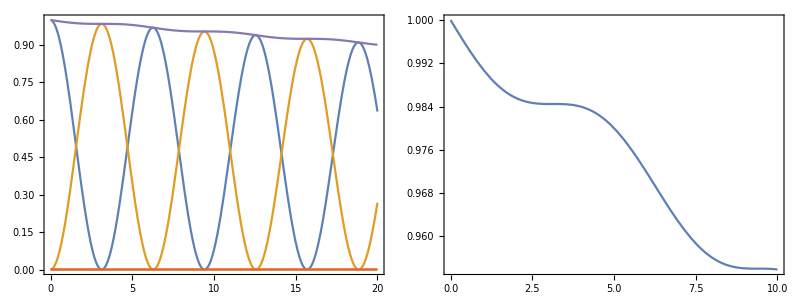

```mathematica
Grid[{
{
Plot[{p0mod["e","upm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["g","upm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["e","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0mod["g","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0totaleUp/.ΩH->1/.γ->0.01},{t,0,20}],

Plot[{p0totaleUp/.ΩH->1/.γ->0.01},{t,0,10}]
}
}]
```

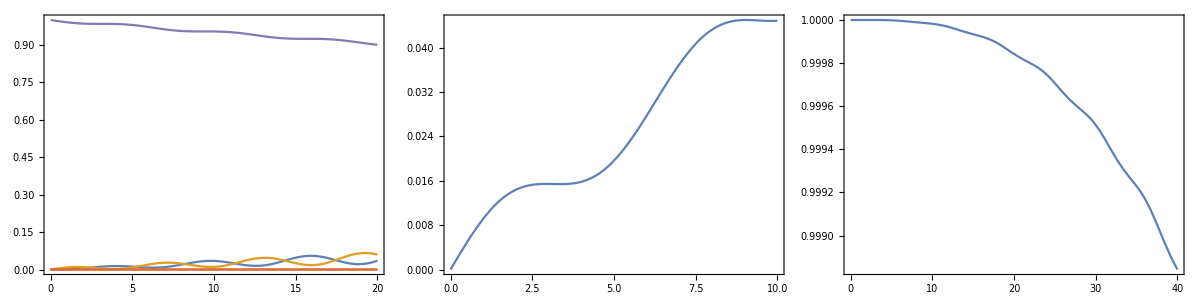

```mathematica
Grid[{
{
Plot[{p1Rmod["e","upm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["g","upm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["e","dwm","e","upm"]/.ΩH->1/.γ->0.01,p1Rmod["g","dwm","e","upm"]/.ΩH->1/.γ->0.01,p0totaleUp/.ΩH->1/.γ->0.01},{t,0,20}],

Plot[{p1RtotaleUp/.ΩH->1/.γ->0.01},{t,0,10}],

Plot[{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->0.01},{t,0,40}]
}
}]
```

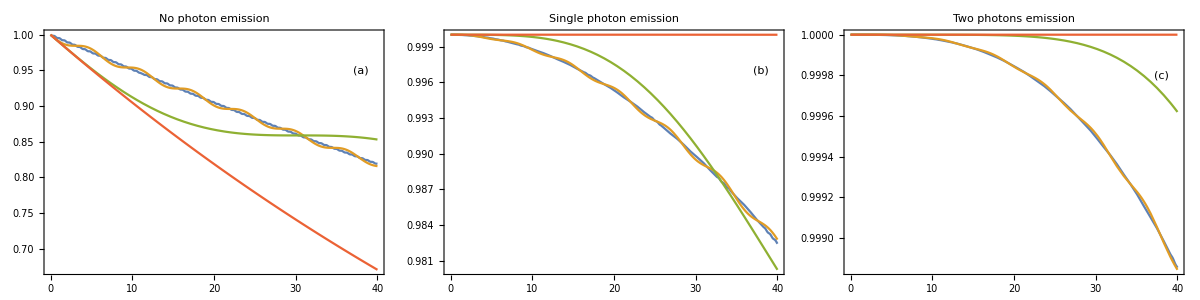

```mathematica
normalizationplots=Grid[{
{
Plot[
{(p0totaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp)/.ΩH->0.001/.γ-> 0.01},{t,0,40},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,0.95}]],

Plot[
{(p0totaleUp+p1RtotaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.001/.γ->0.01},{t,0,40},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,0.997}]
],

Plot[
{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->10/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.1/.γ->0.01,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.001/.γ->0.01},{t,0,40},
PlotRange->All,
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.2,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,0.9998}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck.pdf",normalizationplots];
```

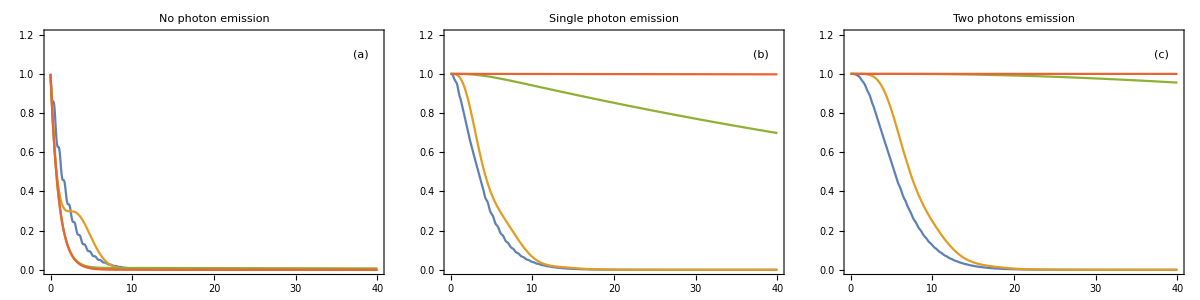

```mathematica
normalizationplots2=Grid[{
{
Plot[
{(p0totaleUp)/.ΩH->10/.γ->1,
(p0totaleUp)/.ΩH->1/.γ->1,
(p0totaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,1.1}]],

Plot[
{(p0totaleUp+p1RtotaleUp)/.ΩH->10/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->1/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp+p1RtotaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,1.1}]
],

Plot[
{(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->10/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->1/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->0.1/.γ->1,
(p0totaleUp+p1RtotaleUp+p1R1RtotaleUp)/.ΩH->8 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.8,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,1.1}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck2.pdf",normalizationplots2];
```

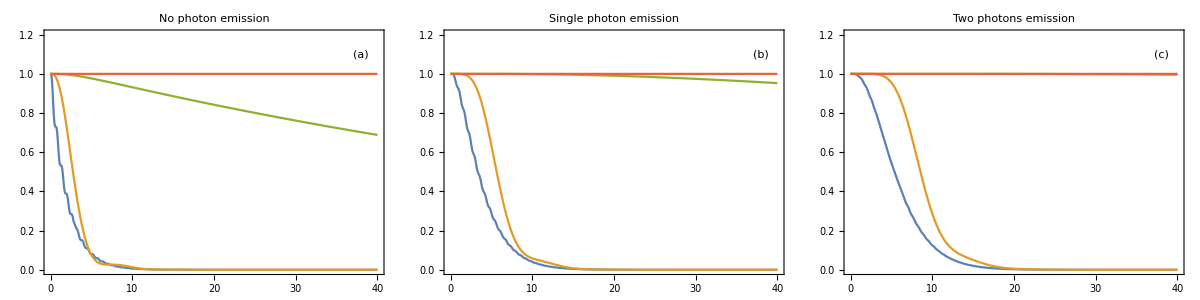

```mathematica
normalizationplot3=Grid[{
{
Plot[
{(p0totalgUp)/.ΩH->10/.γ->1,
(p0totalgUp)/.ΩH->1/.γ->1,
(p0totalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp)/.ΩH->0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"No photon emission",
Epilog->Inset[alphabetlabel[[1]],{38,1.1}]],

Plot[
{(p0totalgUp+p1RtotalgUp)/.ΩH->10/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->1/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp+p1RtotalgUp)/.ΩH->0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Single photon emission",
Epilog->Inset[alphabetlabel[[2]],{38,1.1}]
],

Plot[
{(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->10/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->1/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH->0.1/.γ->1,
(p0totalgUp+p1RtotalgUp+p1R1RtotalgUp)/.ΩH-> 0.001/.γ->1},{t,0,40},
PlotRange->{All,{0.,1.2}},
 PlotLabel->"Two photons emission",
PlotLegends->legend[{MX@"\Omega_H=10",MX@"\Omega_H=1",MX@"\Omega_H=10^{-2}",MX@"\Omega_H= 10^{-3}"},{0.8,0.38}],
Epilog->Inset[alphabetlabel[[3]],{38,1.1}]]
}
}]
Export[PlotsPath<>"NormalizationTruncationCheck2IntialStategUp.pdf",normalizationplot3];
```

### 5) Checking normalization for the simplified model: with spin precesion Ω ≥ 0 (Need to be done numerically)☑

In the last section we turned-off the spin precession Ω and checked the normalization of the driven wave-function truncated at two-photon component, in time for different values of Ω_H. There it was possible to compute the integrals symbolically. In this section I want to verify the same is true, yet for the simplified model adding the precession term. I tried to do it symbolically but it does not seems feasible due to the number of parameters. Hence, I’ll do the same numerically. The next step is check normalization for different Ω_g and Ω_e, i.e. for the real experimental parameters. This will provide us a solid ground to compute the quantities of interest for the experiment.

We have four parameters:
	1)Ω_H the drive,
	2) Ω the precession,
	3) The initial state ϵi,si, and
	4) The final state ϵf,sf

```mathematica
Exp2Ωprecessionlist
```

{0.,0.0771277,0.154255,0.231383,0.347074,0.385638,0.462766,0.694149}

```mathematica
Exp2Ωprecessionlist2={0.07712765957446809,0.15425531914893617};
drivingΩHlist = {10^-3,10^-1,1}//N;
```

```mathematica
PrettyTiming@Do[
PrintTemporary[Ωprecession];
PrintTemporary[Ωdriving];
p0simplifiedtable[ϵf,sf,ϵi,si,Ωprecession,Ωdriving]=Table[{τ,Abs[f0mod[ϵf,sf,ϵi,si,τ]/.γ->1/.ΩH->Ωdriving/.Ω->Ωprecession]^2},{τ,0,20,0.5}],
(*Since there was no emission, the fina state must be the excited one*)
{ϵf,{"e"}},
(*But it can start in any energy state*)
{ϵi,{"e","g"}},
(*With any spin*)
{sf,{"upm","dwm"}},
{si,{"upm","dwm"}},
{Ωprecession,Exp2Ωprecessionlist2},
{Ωdriving,drivingΩHlist}]
```

0h : 1m : 24s

```mathematica
DumpSave["p0simplifiedtable.mx",p0simplifiedtable];
```

```mathematica
Do[

p0simplifiedtableTotal["g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]]=Table[
{p0simplifiedtable["e","dwm","g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]][[i,1]],Sum[p0simplifiedtable[ϵf,sf,"g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]][[i,2]],{ϵf,{"e"}},{sf,{"upm","dwm"}}]},{i,1,Length@p0simplifiedtable["g","dwm","g","dwm",Exp2Ωprecessionlist[[1]],drivingΩHlist[[3]]]}],
{l,1,Length@Exp2Ωprecessionlist},
{m,1,Length@drivingΩHlist}
]
```

Part::partd: Part specification p0simplifiedtable[e,Dw,g,Dw,0.,0.001]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification p0simplifiedtable[e,Up,g,Dw,0.,0.001]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification p0simplifiedtable[e,Dw,g,Dw,0.,0.001]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

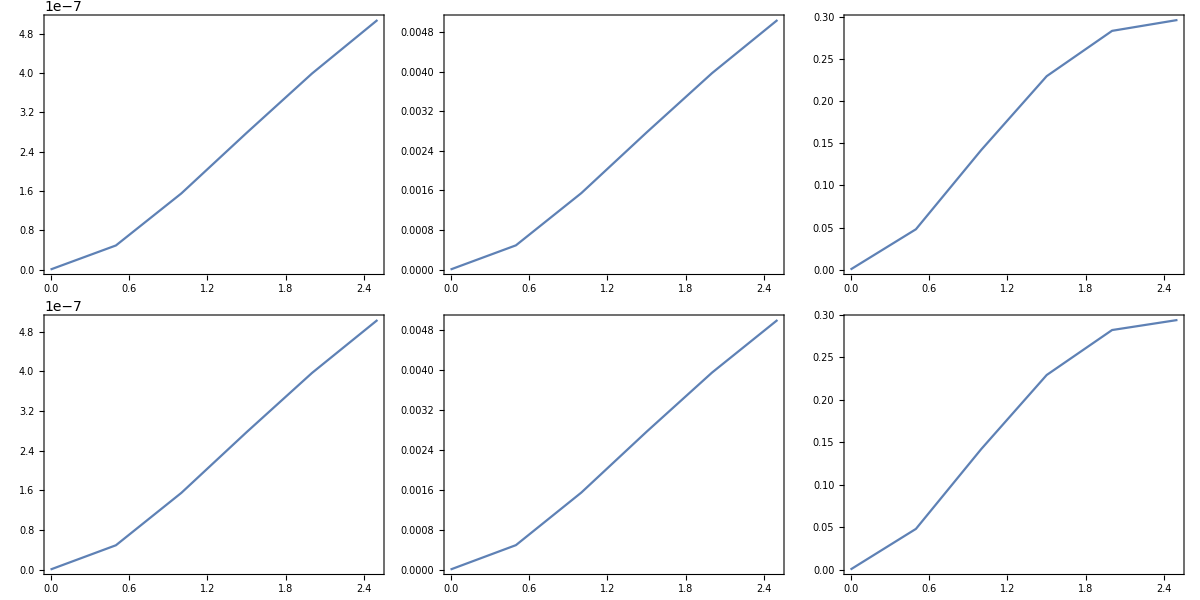

```mathematica
Grid[

Table[
ListLinePlot[
p0simplifiedtableTotal["g","dwm",Exp2Ωprecessionlist[[l]],drivingΩHlist[[m]]],PlotRange->All],
{l,1,Length@Exp2Ωprecessionlist},
{m,1,Length@drivingΩHlist}]



]
```

## III. Spontaneous emission: Analytical calculations and basic plots

In this section I:
	1) Perform some necessary analytical calculations, notably to obtain the probabilities and the spin density matrix state as computed in the paper.

## 1. Ideal case

### 1) Analytics for Intensities and cBhat ☑

```mathematica
IRUpSE=γ Abs[f0SE["e","upm","e", "upm",t]]^2//cf
IRDwSE=γ Abs[f0SE["e","upm","e", "dwm",t]]^2//cf

ILUpSE=γ Abs[f0SE["e","dwm","e", "upm",t]]^2//cf
ILDwSE=γ Abs[f0SE["e","dwm","e", "dwm",t]]^2//cf
```

ⅇ^(-t γ) γ Cos[(t Ω)/2]^2

ⅇ^(-t γ) γ Sin[(t Ω)/2]^2

ⅇ^(-t γ) γ Sin[(t Ω)/2]^2

ⅇ^(-t γ) γ Cos[(t Ω)/2]^2

```mathematica
cBhatSE = √(IRUpSE IRDwSE+ILUpSE ILDwSE)//cf
```

(ⅇ^(-t γ) γ)/(√2 Abs[Csc[t Ω]])

```mathematica
IRUp=γ Abs[f0["e","upm","e", "upm",t]]^2;
IRDw=γ Abs[f0["e","upm","e", "dwm",t]]^2;

ILUp=γ Abs[f0["e","dwm","e", "upm",t]]^2;
ILDw=γ Abs[f0["e","dwm","e", "dwm",t]]^2;
```

```mathematica
(IRUpSE-ILUpSE)/(IRUpSE+ILUpSE)//cf
```

Cos[t Ω]

```mathematica
(IRDwSE-ILDwSE)/(IRDwSE+ILDwSE)//cf
```

-Cos[t Ω]

```mathematica
cBhat = √(IRUpSE IRDwSE+ILUpSE ILDwSE);
```

Wait the time exactly equal to the period in the ideal case tΩe=π.

```mathematica
cBhatSE /.t->π/(Ω)
```

0

### 1a: Exp.1: Intensities and contrast. Data x Ideal Model. Reproduction of Fig 2 of a published paper as a sanity check of the model. ☑

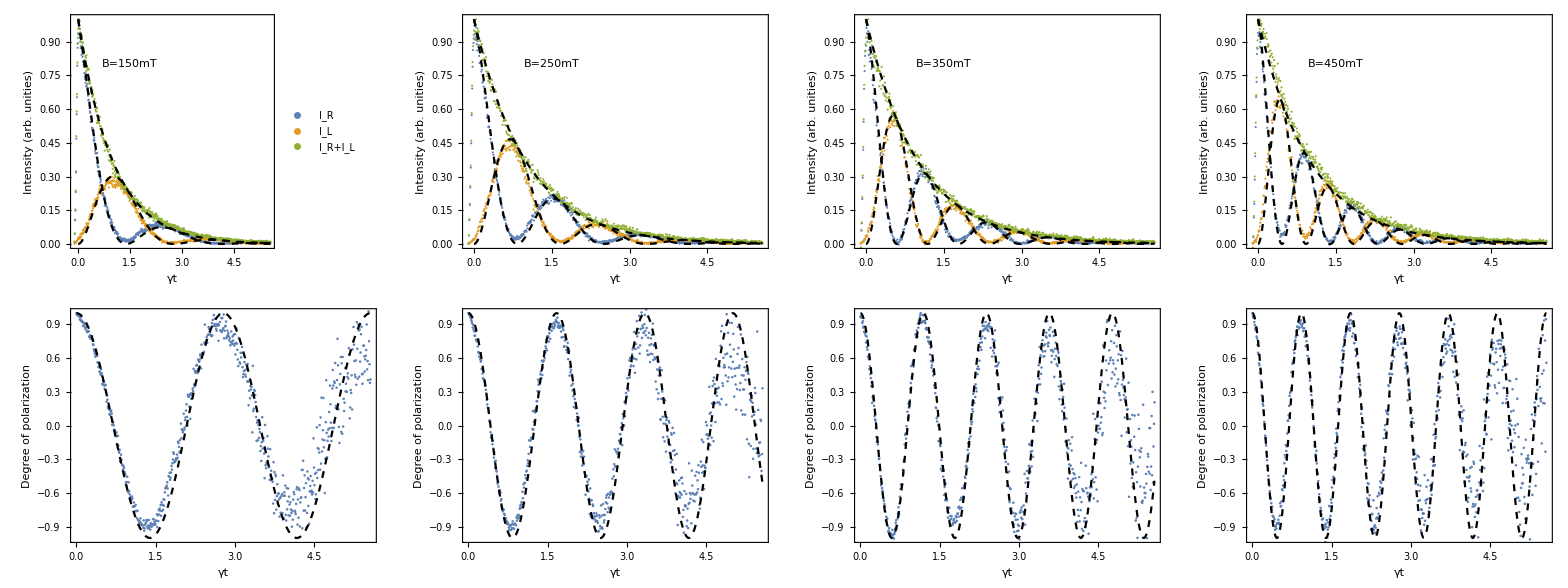

```mathematica
Clear[DCP];
texperimental = 5.56;(*Used to keep γ=1*)
(*Degre of circular polarization*)
DCP=(IRUpSE-ILUpSE)/(IRUpSE+ILUpSE)//cf;

Module[{timescaling,dataset1,dataset2,physicalparameters,epilog},
timescaling =5.56/2.5 (*Used to keep γ=1*);
dataset1=dataexp1list;
dataset2=datadcplist;
epilog={"B=150mT","B=250mT","B=350mT","B=450mT"};
physicalparameters=Exp1physicalparameterslist;
Fig0=Grid[{
(*First row*)
Table[
Show[
ListPlot[{
Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,2⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling,dataset1[[k]]⟦i,3⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,4⟧},{i,1,Length@dataset1[[k]]}]},
PlotRange->{All,{0,1}},
PlotLegends->If[k==1,legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],None],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[epilog[[k]]],Background->LightYellow],{1.5,0.8}]],

Plot[{IRUpSE/.physicalparameters[[k]],
ILUpSE/.physicalparameters[[k]],
IRUpSE+ILUpSE/.physicalparameters[[k]]},
{t,0,texperimental},

PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed}},
PlotRange->{All,{0,1}},
PlotLegends->legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[k],Background->LightYellow],{1.5,0.8}]]
],
{k,1,Length@dataset1}],

(*Second row*)
Table[
Show[
ListPlot[
Table[{dataset2[[k]]⟦i,1⟧*(5.56/2.5),
           dataset2[[k]]⟦i,2⟧},{i,1,Length@dataset2[[k]]}],
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}],

Plot[DCP/.physicalparameters[[k]],{t,0,texperimental},
PlotStyle->{{Black, Dashed}},
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}]],
{k,1,Length@dataset2}
]
}]
]
Export[PlotsPathChap6<>"Fig0-Exp1DatavsModelSE.pdf",Fig0];
```

This figure is important as it shows perfect agreement between the model, represented by the dashed black lines, and the actual data points. The model is accurate. It does not capture the dephasing in the DCP, because as it only depends on Ωe., still quantitatively it matches perfect.

### 1b: Plot of Intensities for both experiments ☑

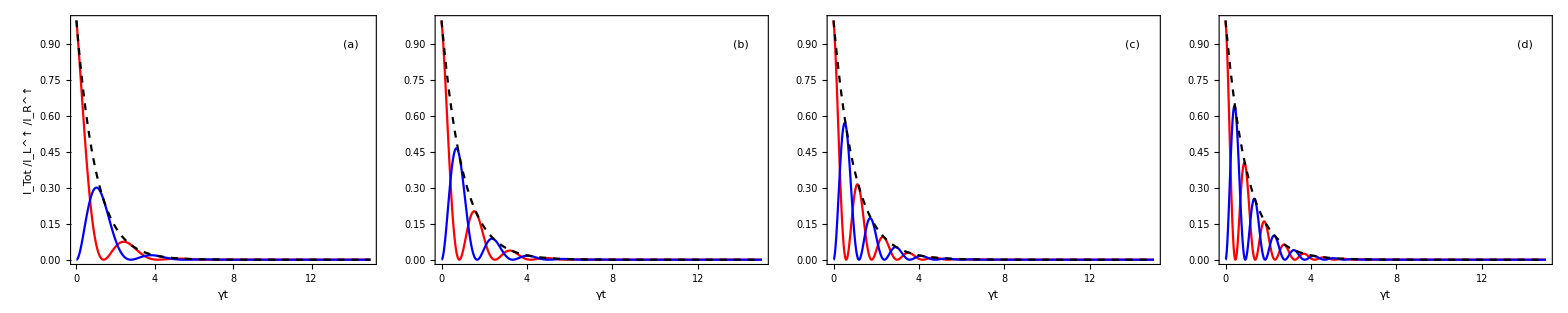

```mathematica
Module[{physicalparameters},
physicalparameters=Exp1physicalparameterslist;
Fig1 = Grid[{

Table[
Plot[{IRUpSE/.γ->1/.physicalparameters[[k]],ILUpSE/.γ->1/.physicalparameters[[k]],ILUpSE+IRUpSE/.γ->1/.physicalparameters[[k]]},{t,0,15},
FrameLabel->If[k==1,{"γt",Style["I_Tot",Black] Style["/I_R^↑",Red]Style["/I_L^↑",Blue]},{"γt", ""}],
PlotRange->{{0.,All},{0,1.05}},
PlotStyle->{Red,Blue,{Black,Dashed}},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig1-IntensitiesExp1SE.pdf",Fig1];
```

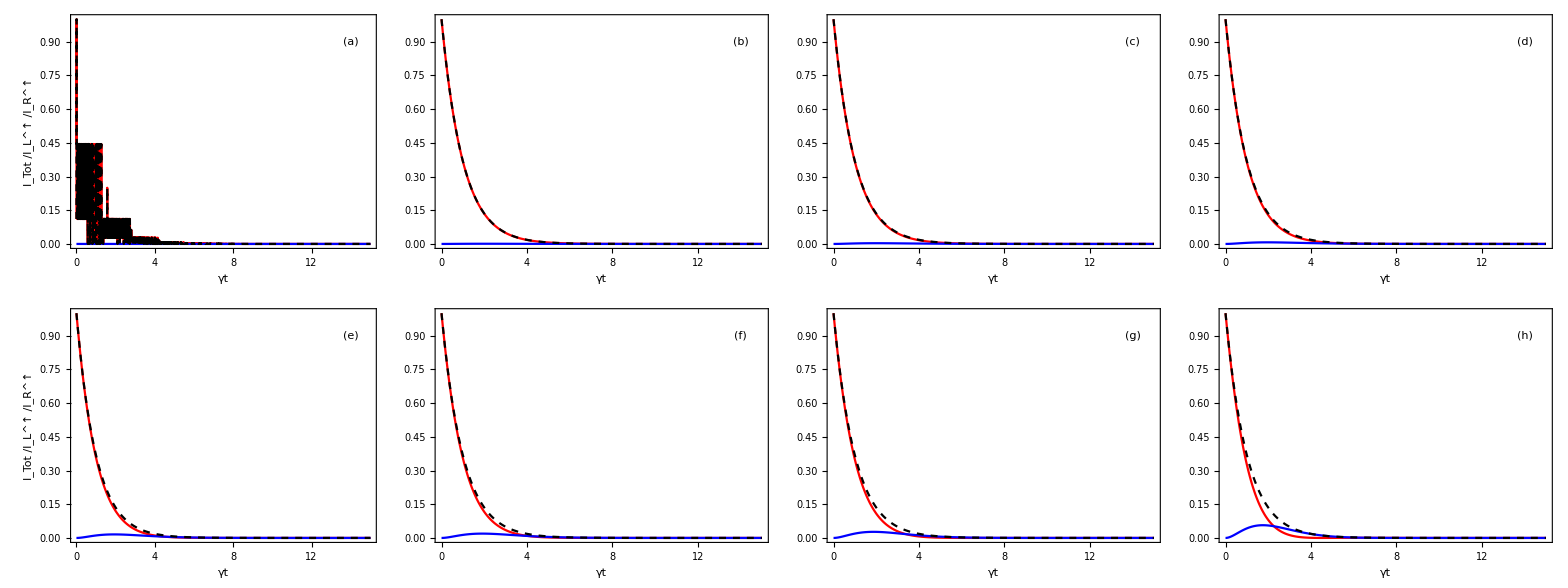

```mathematica
Module[{physicalparameters,ΩH},
physicalparameters=Exp2physicalparameterslist;
ΩH=8 10^-3;
Fig2=Grid[{

Table[
Plot[{IRUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,ILUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,ILUp+IRUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH},{t,0,15},
FrameLabel->If[k==1,{"γt",Style["I_Tot",Black] Style["/I_R^↑",Red]Style["/I_L^↑",Blue]},{"γt", ""}],
PlotRange->{{0.,All},{0,1.05}},
PlotStyle->{Red,Blue,{Black,Dashed}},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,1,Length@physicalparameters/2}],

Table[
Plot[{IRUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,ILUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,ILUp+IRUp/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH},{t,0,15},
FrameLabel->If[k==Length@physicalparameters/2+1,{"γt",Style["I_Tot",Black] Style["/I_R^↑",Red]Style["/I_L^↑",Blue]},{"γt", ""}],
PlotRange->{{0.,All},{0,1.05}},
PlotStyle->{Red,Blue,{Black,Dashed}},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,Length@physicalparameters/2+1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig2-IntensitiesExp2.pdf",Fig2];
```

### 1c: Plot of cBhat for both experiments ☑

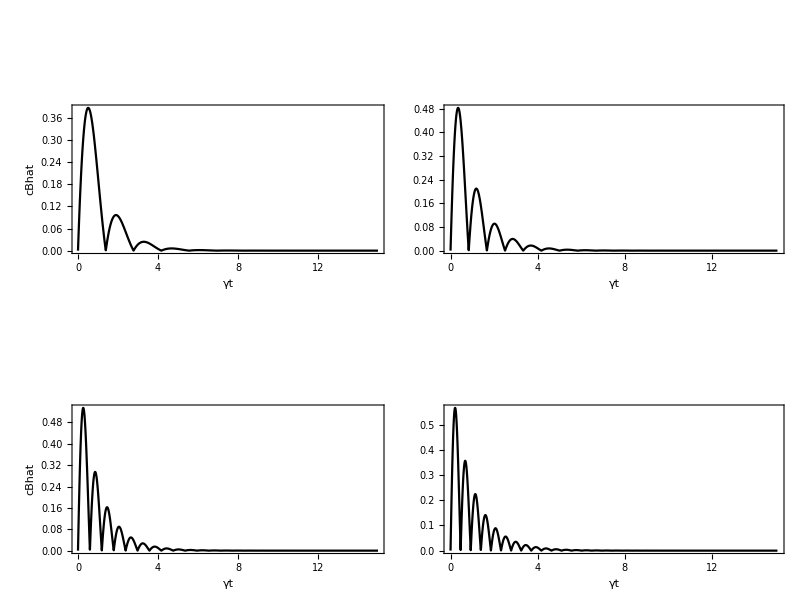

```mathematica
Module[{physicalparameters,function},
physicalparameters=Exp1physicalparameterslist;
function=cBhatSE;
Fig3=Grid[{

Table[
Plot[function/.physicalparameters[[k]],{t,0,15},
FrameLabel->If[k==1,{"γt","cBhat"},{"γt", ""}],
PlotRange->{{0.,All},{0,1.05}},
PlotStyle->{Black},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,1,Length@physicalparameters/2}],

Table[
Plot[function/.physicalparameters[[k]],{t,0,15},
FrameLabel->If[k==Length@physicalparameters/2+1,{"γt","cBhat"},{"γt", ""}],
PlotRange->{{-0.1,All},{0,1.05}},
PlotStyle->{Black},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,Length@physicalparameters/2+1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig3-cBhatExp1.pdf",Fig3];
```

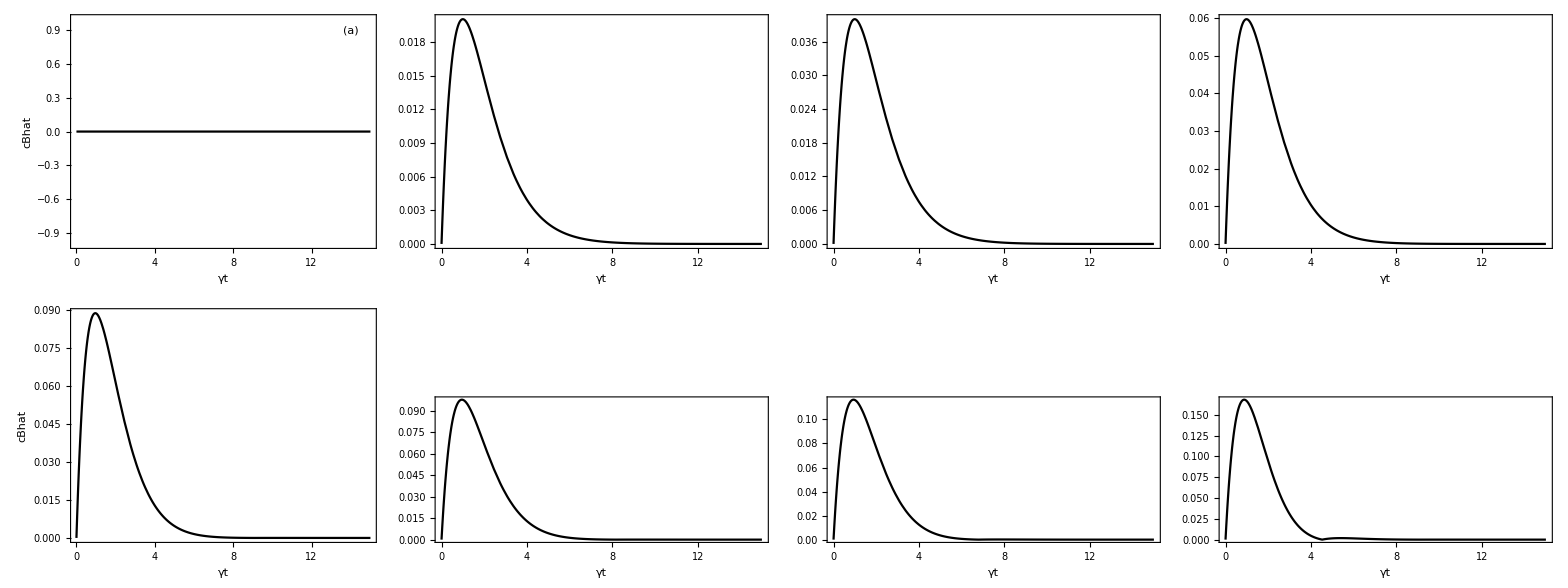

```mathematica
Module[{physicalparameters,function,ΩH},
physicalparameters=Exp2physicalparameterslist;
function=cBhat;
ΩH=8 10^-3;
Fig4=Grid[{

Table[
Plot[function/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,{t,0,15},
FrameLabel->If[k==1,{"γt","cBhat"},{"γt", ""}],
PlotRange->{{0.,All},{0,1.05}},
PlotStyle->{Black},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,1,Length@physicalparameters/2}],

Table[
Plot[function/.physicalparameters[[k]]/.MagneticFieldDirection/.ΩL->ΩH/.ΩR->ΩH,{t,0,15},
FrameLabel->If[k==Length@physicalparameters/2+1,{"γt","cBhat"},{"γt", ""}],
PlotRange->{{-0.1,All},{0,1.05}},
PlotStyle->{Black},
Epilog->Inset[alphabetlabel[[k]],{14,0.9}]],
{k,Length@physicalparameters/2+1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig4-cBhatExp2.pdf",Fig4];
```

### 2) Analytics for all probabilities: Spontaneous emission ☑

In this section I compute all the probabilities that the wavefunction gives me and also I perform some sanity checks.

All the calculations are done for an initial spin Up, because the experiments we’re interested in fitting are prepared in this way.

```mathematica
P0eUpSE=f0SE["e","upm", "e", "upm",t]f0SE["e","upm", "e", "upm",t]*//cf
```

ⅇ^(-t γ) Cos[(t Ω)/2]^2

```mathematica
ampRgUpSE= f1RSE["g","upm", "e", "upm",t,t1]f1RSE["g","upm", "e", "upm",t,t1]*//cf
PrettyTiming[P1RgUptSE=Integrate[ampRgUpSE,{t1,0,t}]/.nx^2+ny^2->(1-nz^2)]
```

1/2 ⅇ^(-t1 γ) Cos[(t1 Ω)/2]^2 (1+nz^2-(-1+nz^2) Cos[(t-t1) λ Ω])

0h : 0m : 15s

1/2 (-(-1+ⅇ^(-t γ))/(2 γ)-((-1+ⅇ^(-t γ)) nz^2)/(2 γ)+(-1+ⅇ^(t (-γ-ⅈ Ω)))/(4 (-γ-ⅈ Ω))+((-1+ⅇ^(t (-γ-ⅈ Ω))) nz^2)/(4 (-γ-ⅈ Ω))+(-1+ⅇ^(t (-γ+ⅈ Ω)))/(4 (-γ+ⅈ Ω))+((-1+ⅇ^(t (-γ+ⅈ Ω))) nz^2)/(4 (-γ+ⅈ Ω))+(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ λ Ω))))/(4 (-γ-ⅈ λ Ω))-(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ λ Ω))) nz^2)/(4 (-γ-ⅈ λ Ω))+(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω-ⅈ λ Ω))))/(8 (-γ-ⅈ Ω-ⅈ λ Ω))-(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω-ⅈ λ Ω))) nz^2)/(8 (-γ-ⅈ Ω-ⅈ λ Ω))+(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω-ⅈ λ Ω))))/(8 (-γ+ⅈ Ω-ⅈ λ Ω))-(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω-ⅈ λ Ω))) nz^2)/(8 (-γ+ⅈ Ω-ⅈ λ Ω))+(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ λ Ω))))/(4 (-γ+ⅈ λ Ω))-(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ λ Ω))) nz^2)/(4 (-γ+ⅈ λ Ω))+(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω+ⅈ λ Ω))))/(8 (-γ-ⅈ Ω+ⅈ λ Ω))-(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω+ⅈ λ Ω))) nz^2)/(8 (-γ-ⅈ Ω+ⅈ λ Ω))+(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω+ⅈ λ Ω))))/(8 (-γ+ⅈ Ω+ⅈ λ Ω))-(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω+ⅈ λ Ω))) nz^2)/(8 (-γ+ⅈ Ω+ⅈ λ Ω)))

```mathematica
ampLgUpSE=f1LSE["g","upm", "e", "upm",t,t1]f1LSE["g","upm", "e", "upm",t,t1]*/.(nx^2+ny^2)->1-nz^2//cf
PrettyTiming[P1LgUptSE=Integrate[ampLgUpSE,{t1,0,t}]/.(nx^2+ny^2)->1-nz^2]
```

ⅇ^(-t1 γ) (nx^2+ny^2) Sin[(t1 Ω)/2]^2 Sin[1/2 (t-t1) λ Ω]^2

0h : 0m : 36s

(1-nz^2) (-(-1+ⅇ^(-t γ))/(4 γ)-(-1+ⅇ^(t (-γ-ⅈ Ω)))/(8 (-γ-ⅈ Ω))-(-1+ⅇ^(t (-γ+ⅈ Ω)))/(8 (-γ+ⅈ Ω))-(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ λ Ω))))/(8 (-γ-ⅈ λ Ω))+(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω-ⅈ λ Ω))))/(16 (-γ-ⅈ Ω-ⅈ λ Ω))+(ⅇ^(ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω-ⅈ λ Ω))))/(16 (-γ+ⅈ Ω-ⅈ λ Ω))-(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ λ Ω))))/(8 (-γ+ⅈ λ Ω))+(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ-ⅈ Ω+ⅈ λ Ω))))/(16 (-γ-ⅈ Ω+ⅈ λ Ω))+(ⅇ^(-ⅈ t λ Ω) (-1+ⅇ^(t (-γ+ⅈ Ω+ⅈ λ Ω))))/(16 (-γ+ⅈ Ω+ⅈ λ Ω)))

```mathematica
PUptSE =P0eUpSE+P1RgUptSE+P1LgUptSE/.(nx^2+ny^2)->1-nz^2//cf
```

1/8 (4/γ+(4 ⅇ^(-t γ) (-1+γ))/γ+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) (-2 γ^2+4 ⅈ γ Ω-2 (-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))+4 ⅇ^(-t γ) Cos[t Ω])

Sanity checks: Is the wave-function properly normalized?

```mathematica
(P0eUpSE+P0eDwSE+P1RgUptSE+P1RgDwtSE+P1LgUptSE+P1LgDwtSE-1//cf)==0
```

True

```mathematica
PUpt+PDwt//cf
```

1

```mathematica
ProbabilityOfEmission=PUpgt+PDwgt//cf
```

1-ⅇ^(-t γ)

```mathematica
ProbabilityOfExcitedState=P0eUp+P0eDw//cf
```

ⅇ^(-t γ)

### 2a: Plot of probabilities up and down in the ground state and R and L emissions ☑

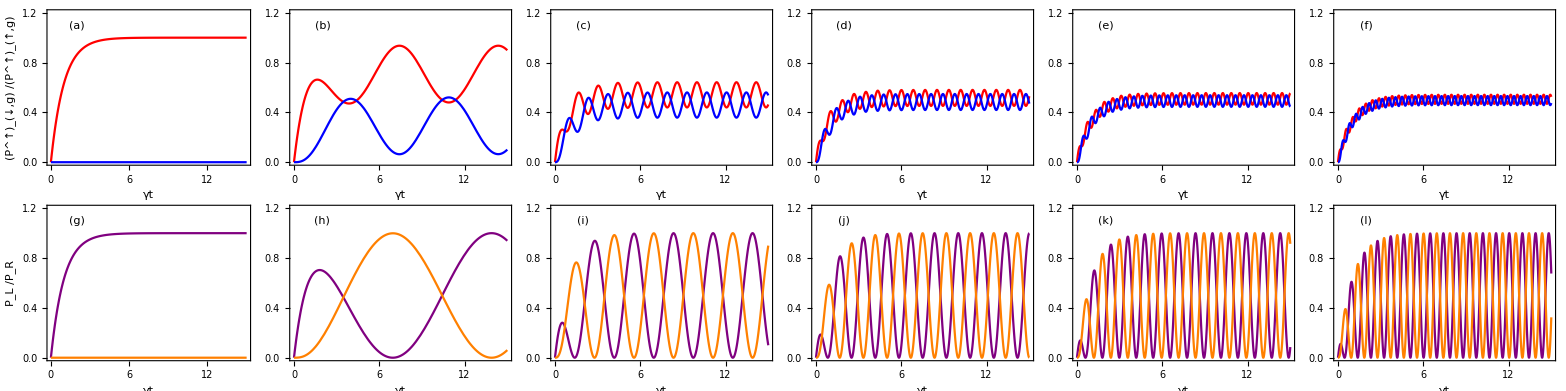

```mathematica
Module[{FunctionToPlot,physicalparameters,FunctionToPlot2},
physicalparameters=Exp1physicalparameterslist;

Fig3= Grid[
{
Table[
FunctionToPlot={PUpgt/.physicalparameters[[k]]/.MagneticFieldDirection//cf,PDwgt/.physicalparameters[[k]]/.MagneticFieldDirection//cf};

Plot[FunctionToPlot,{t,0,15 },
PlotRange->{All,{0,1.2}},
PlotStyle->{Red,Blue},
FrameLabel->If[k==1,{"γt", Style["/(P^↑)_(↑,g)",Red]Style["(P^↑)_(↓,g)",Blue]},{"γt", "    "}],
Epilog->Inset[alphabetlabel[[k]],{2,1.1}]
],
{k,1,Length@physicalparameters}],

Table[
FunctionToPlot2={PRt/.physicalparameters[[k]]/.MagneticFieldDirection//cf,PLt/.physicalparameters[[k]]/.MagneticFieldDirection//cf};

Plot[FunctionToPlot2,{t,0,15 },
PlotRange->{All,{0,1.2}},
PlotStyle->{Purple,Orange,{Black,Dashed}},
PlotRange->{{-0.,40},{-0,2}},
FrameLabel->If[k==1,{"γt", Style["/P_R",Purple]Style["P_L",Orange]},{"γt", "    "}],
Epilog->Inset[alphabetlabel[[Length@physicalparameters+k]],{2,1.1}]
],

{k,1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig3ProbabilitiesUpDownRandL-Exp1.pdf",Fig3];
```

```mathematica
texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)

Module[{FunctionToPlot,physicalparameters,FunctionToPlot2},
physicalparameters=Exp2physicalparameterslist;

Fig4=Grid[
{
Table[
FunctionToPlot={PUpgt/.physicalparameters[[k]]/.MagneticFieldDirection//cf,PDwgt/.physicalparameters[[k]]/.MagneticFieldDirection//cf};

Plot[FunctionToPlot,{t,0,texperimentalg2 },
PlotRange->{All,{0,1.2}},
PlotStyle->{Red,Blue},
FrameLabel->If[k==1,{"γt", Style["/(P^↑)_(↑,g)",Red]Style["(P^↑)_(↓,g)",Blue]},{"γt", "    "}],
Epilog->Inset[alphabetlabel[[k]],{2,1.1}]
],
{k,1,Length@physicalparameters}],

Table[
FunctionToPlot2={PRt/.physicalparameters[[k]]/.MagneticFieldDirection//cf,PLt/.physicalparameters[[k]]/.MagneticFieldDirection//cf};

Plot[FunctionToPlot2,{t,0,texperimentalg2 },
PlotRange->{All,{0,1.2}},
PlotStyle->{Purple,Orange,{Black,Dashed}},
PlotRange->{{-0.,40},{-0,2}},
FrameLabel->If[k==1,{"γt", Style["/P_R",Purple]Style["P_L",Orange]},{"γt", "    "}],
Epilog->Inset[alphabetlabel[[Length@physicalparameters+k]],{2,1.1}]
],

{k,1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig4ProbabilitiesUpDownRandL-Exp2.pdf",Fig4];
```

### 3) Spin state at time t: Analytical calculations ☑

```mathematica
<<overlapsforSpinState.mx
```

In this section I:
	1) Perform the integrals to obtain the matrix elements of the spin density matrix analytically;
	2) Obtain the eigenvalues of the density matrix at time t rotated by a general unitary;

Mathematica has some problem with understanding that some parameters are real, so when we conjugate something it considers everything as a complex number. That’s why I write all the expressions explicitly and use the cf command (from Melt!) to FullSimplify considering the parameters real. If I don’t do this, Mathematica simply doesn’t perform the necessary integrals.

Below I compute all the overlaps for all times, that’s to say, I’m not simplifying to the long time limit, so all the expressions below DO HAVE the excited state component.

```mathematica
ℛe[t]//mf;
```

(Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2] | 0 | 0
-ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2] | 0 | 0
0 | 0 | Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2]
0 | 0 | -ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2])

```mathematica
PrettyTiming[
Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2,FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t] (ket["e", "upm"]*.ℛe[t].ket["e", "upm"])*ket["e", "upm"]*.ℛe[t].ket["e", "upm"] //cf;(*✓*)

SecondTerm=(ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"]//cf;(*✓*)
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)

PrettyTiming[FirstIntegral=Integrate[SecondTerm Product1//cf,{u,0,t}]];
PrettyTiming[SecondIntegral= Integrate[ThirdTerm Product2//cf,{u,0,t}]];

ℴUpUp = FirstTerm +γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
ℴUpUpg = γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
]
]
```

0h : 0m : 16s

0h : 0m : 39s

0h : 5m : 54s

```mathematica
ℴUpUp
```

1/4 (2+(ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(2 nz^2 γ^2)/(γ^2+Ω^2)-(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω+Ω^2-λ^2 Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (-γ^2+2 ⅈ γ Ω+Ω^2-nz^2 λ^2 Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))+2 ⅇ^(-t γ) Cos[t Ω])

```mathematica
ℴUpUpg
```

1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))

```mathematica
PrettyTiming[
Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2,FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t] (ket["e", "dwm"]*.ℛe[t].ket["e", "upm"])*ket["e", "dwm"]*.ℛe[t].ket["e", "upm"]//cf;(*✓*)

SecondTerm=(ket["g","dwm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "dwm"]*.ℛg[t-u].ket["g", "upm"]//cf;(*✓*)
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"])*ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)
FirstIntegral = Integrate[(SecondTerm Product1)//cf,{u,0,t}];
SecondIntegral = Integrate[(ThirdTerm Product2)//cf,{u,0,t}];

ℴDwDw = FirstTerm +γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);

ℴDwDwg =γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
]
]
```

0h : 7m : 34s

```mathematica
ℴDwDw
```

1/8 (4-(4 nz^2 γ^2)/(γ^2+Ω^2)-4 ⅇ^(-t γ) Cos[t Ω]+(4 ⅇ^(-t γ) γ (γ (γ^4+γ^2 (2+(1+nz^2) λ^2) Ω^2+(1+λ^2+nz^2 λ^2 (-3+λ^2)) Ω^4) Cos[t Ω]-Ω (γ^4+γ^2 (2+(-1+3 nz^2) λ^2) Ω^2+(-1+λ^2) (-1+nz^2 λ^2) Ω^4) Sin[t Ω]+ⅇ^(t γ) (-1+nz^2) (γ^2+Ω^2) (γ (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]+λ Ω (γ^2+(-1+λ^2) Ω^2) Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)))

```mathematica
ℴDwDwg
```

1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))

```mathematica
PrettyTiming[

Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2, FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t](ket["e", "dwm"]*.ℛe[t].ket["e", "upm"])*ket["e", "upm"]*.ℛe[t].ket["e", "upm"]//cf;(*✓*)

SecondTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"]//cf;
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"])* ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓-There was a correction here! The not conjugated part was swaped the Up and Dw*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)

FirstIntegral = Integrate[(SecondTerm Product1)//cf,{u,0,t}];
SecondIntegral = Integrate[(ThirdTerm Product2)//cf,{u,0,t}];

ℴDwUp = FirstTerm+γ(FirstIntegral+SecondIntegral)//cf;

ℴDwUpg = γ(FirstIntegral+SecondIntegral)//cf;

]
]
```

0h : 11m : 38s

```mathematica
ℴDwUp
```

1/4 (2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))

```mathematica
ℴDwUpg
```

-((ⅇ^(-2 t γ+ⅈ t (-1+λ) Ω) (nx-ⅈ ny) γ (ⅇ^(2 t γ+ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(t (2 γ+ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ-ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ-ⅈ λ Ω)) λ (γ-ⅈ Ω) Ω (-ⅈ γ+Ω+nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ-ⅈ (-2+λ) Ω)) λ (γ+ⅈ Ω) Ω (-ⅈ γ+(-1+nz λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

```mathematica
ℴUpDw=Conjugate[ℴDwUp]
```

1/4 Conjugate[2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6)]

Yeah, Mathematica doesn’t conjugate smartly. We have to outsmart Mathematica, below I do it by hand:

```mathematica
ℴUpDw=1/4 (-2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx+ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (-ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((ⅈ γ^4+nz γ^3 λ Ω+ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3+ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (-2 ⅈ γ^3-3 nz γ^2 λ Ω-2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (ⅈ γ^3+nz γ^2 λ Ω+ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))
```

1/4 (-2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx+ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (-ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((ⅈ γ^4+nz γ^3 λ Ω+ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3+ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (-2 ⅈ γ^3-3 nz γ^2 λ Ω-2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (ⅈ γ^3+nz γ^2 λ Ω+ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))

```mathematica
ℴUpDwg=-((ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ+ⅈ Ω) (γ-ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)+ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ+ⅈ Ω) (γ-ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))
```

-((ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

As it takes a lot of time to compute these overlaps I’ll save them:

```mathematica
DumpSave["overlapsforSpinState.mx",{ℴUpUp,ℴDwDw,ℴDwUp,ℴUpDw,ℴUpUpg,ℴDwDwg,ℴDwUpg,ℴUpDwg}];
```

### 4) Computing the fidelity at time t_r = π/(2λΩ) - Working here

```mathematica
<<AnalyticalExpressionOfTheFidelity.mx
```

The density matrix for the mathematical spin, i.e., the one considering the decay as well, is given by:

```mathematica
ρmathematicalspin =({{ℴUpUp, ℴDwUp}, {ℴUpDw, ℴDwDw}})//mf;
```

(1/4 (2+(ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(2 nz^2 γ^2)/(γ^2+Ω^2)-(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω+Ω^2-λ^2 Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (-γ^2+2 ⅈ γ Ω+Ω^2-nz^2 λ^2 Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))+2 ⅇ^(-t γ) Cos[t Ω]) | 1/4 (2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))
1/4 Conjugate[2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6)] | 1/8 (4-(4 nz^2 γ^2)/(γ^2+Ω^2)-4 ⅇ^(-t γ) Cos[t Ω]+(4 ⅇ^(-t γ) γ (γ (γ^4+γ^2 (2+(1+nz^2) λ^2) Ω^2+(1+λ^2+nz^2 λ^2 (-3+λ^2)) Ω^4) Cos[t Ω]-Ω (γ^4+γ^2 (2+(-1+3 nz^2) λ^2) Ω^2+(-1+λ^2) (-1+nz^2 λ^2) Ω^4) Sin[t Ω]+ⅇ^(t γ) (-1+nz^2) (γ^2+Ω^2) (γ (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]+λ Ω (γ^2+(-1+λ^2) Ω^2) Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))))

The density matrix of the spin state, i.e., the decay is completed is given by:

```mathematica
ρspin =({{ℴUpUpg, ℴDwUpg}, {ℴUpDwg, ℴDwDwg}})//mf;
```

(1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))) | -(ⅇ^(-2 t γ+ⅈ t (-1+λ) Ω) (nx-ⅈ ny) γ (ⅇ^(2 t γ+ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(t (2 γ+ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ-ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ-ⅈ λ Ω)) λ (γ-ⅈ Ω) Ω (-ⅈ γ+Ω+nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ-ⅈ (-2+λ) Ω)) λ (γ+ⅈ Ω) Ω (-ⅈ γ+(-1+nz λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))
-(ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)) | 1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))))

```mathematica
Tr[%]//cf
```

Tr[1-ⅇ^(-t γ)]

```mathematica
ρspin =ρspin/Tr[ρspin];
```

```mathematica
Tr[%]//cf
```

1

Assuming we had a click in R, the spin in initially up. Under the action of the magnetic field in the σx direction, without any perturbation, the state of the system in a time t=π/(2λ Ω) evolves to the target state:

```mathematica
ψtarget = MatrixExp[-ⅈ (λ Ω)/2 σx t].Basis[2,1]/.t->π/(2λ Ω)//mf;
ρtarget = out[ψtarget,ψtarget†]//mf;
```

(1/(√2)
-ⅈ/(√2))

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

A generic density matrix of a qubit can be written as:

```mathematica
ρgen =(Eye[2]+rx σx + ry σy + rz σz)/2//mf;
```

((1+rz)/2 | 1/2 (rx-ⅈ ry)
1/2 (rx+ⅈ ry) | (1-rz)/2)

The fidelity is easy computed between our target (at time t=π/2rΩ, with r=1) and the general state:

```mathematica
ℱ = QuantumFidelity[ρgen,ρtarget]//cf
```

(1-ry)/2

where

```mathematica
Tr[σy.ρgen]//cf
```

ry

So we have a way of obtaining an analytic expression for the fidelity, which is given by:

```mathematica
ℱanalytical = (1-Tr[σy.ρspin])/2//cf
```

(ⅇ^(-t (γ+ⅈ λ Ω)) (ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
ℱanalytical/.t->π/(2 λ Ω)//cf
```

-((ⅈ ⅇ^(-(π γ)/(2 λ Ω)) (ⅇ^((π (γ-ⅈ Ω))/(2 λ Ω)) γ λ Ω (ⅈ γ+Ω) (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)-2 ⅈ ⅇ^((π γ)/(2 λ Ω)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)+2 ⅈ ⅇ^((π γ)/(λ Ω)) ((1+nx-ny nz) γ^6+ny nz γ^5 λ Ω+γ^4 (3+2 λ^2-2 ny nz (1+λ^2)+nx (2+λ^2)) Ω^2+ny nz γ^3 λ^3 Ω^3+γ^2 (3+λ^4-ny nz (-1+λ^2)^2+nx (1+λ^2)) Ω^4+ny nz γ λ (-1+λ^2) Ω^5+(-1+λ^2)^2 Ω^6)+ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2) (ⅈ ny nz λ Ω+nx (ⅈ γ+Ω))))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

```mathematica
derivativeℱanalytical=D[ℱanalytical, t]
```

-((ⅇ^(t γ-t (γ+ⅈ λ Ω)) γ (ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ))^2 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))+(ⅇ^(-t (γ+ⅈ λ Ω)) (-γ-ⅈ λ Ω) (ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)) (2 ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω)^2 (γ-ⅈ (1+λ) Ω)+2 ⅇ^(2 t γ) (nx-ⅈ ny nz) γ^2 (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) (2 γ+ⅈ λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ+ⅈ λ Ω) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (γ+ⅈ (-1+λ) Ω) (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ+ⅈ (1+λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

Let’s save this nice expression:

```mathematica
DumpSave["AnalyticalExpressionOfTheFidelity.mx",{ℱanalytical,derivativeℱanalytical}];
```

```mathematica
derivativeℱanalytical/.t->π/(2λ Ω)
```

-((ⅇ^((π γ)/(2 λ Ω)-(π (γ+ⅈ λ Ω))/(2 λ Ω)) γ (ⅇ^((π (γ+ⅈ λ Ω))/(λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^((π γ)/(λ Ω)) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^((ⅈ π)/2+(π γ)/(λ Ω)) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^((π (γ+ⅈ λ Ω))/(2 λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^((π (γ+ⅈ (-1+λ) Ω))/(2 λ Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ (1+λ) Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω)))^2 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))+(ⅇ^(-(π (γ+ⅈ λ Ω))/(2 λ Ω)) (-γ-ⅈ λ Ω) (ⅇ^((π (γ+ⅈ λ Ω))/(λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^((π γ)/(λ Ω)) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^((ⅈ π)/2+(π γ)/(λ Ω)) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^((π (γ+ⅈ λ Ω))/(2 λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^((π (γ+ⅈ (-1+λ) Ω))/(2 λ Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ (1+λ) Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-(π (γ+ⅈ λ Ω))/(2 λ Ω)) (2 ⅇ^((π (γ+ⅈ λ Ω))/(λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω)^2 (γ-ⅈ (1+λ) Ω)+2 ⅇ^((π γ)/(λ Ω)) (nx-ⅈ ny nz) γ^2 (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^((ⅈ π)/2+(π γ)/(λ Ω)) (2 γ+ⅈ λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^((π (γ+ⅈ λ Ω))/(2 λ Ω)) (γ+ⅈ λ Ω) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^((π (γ+ⅈ (-1+λ) Ω))/(2 λ Ω)) γ λ (γ-ⅈ Ω) Ω (γ+ⅈ (-1+λ) Ω) (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ (1+λ) Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ+ⅈ (1+λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

The most ideal case happens when there is no difference between the Larmor frequencies, Ω=1, the magnetic field points only in the x-direction (1,0,0). 
In this letting the spin state evolve to time t=π/(2λΩ)=π/(2Ω), we can compute the fidelity between the real and the target states,

```mathematica
idealParameters={nx->1,ny->0,nz->0,γ->1,λ->1};
```

```mathematica
ℱanalytical/.{t->π/(2Ω),γ->1}//cf//Expand
```

```mathematica
idependentofn = -Ω^6/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) Ω^6)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(λ^2 Ω^6)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) λ^2 Ω^6)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(λ^4 Ω^6)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) λ^4 Ω^6)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(λ^4 Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) λ^4 Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-1/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω))/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(λ^2 Ω^2)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) λ^2 Ω^2)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf
dependentonnx =-(nx λ Ω^2)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ^3 Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ^3 Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ^2 Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(nx λ Ω^4)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ^2 Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ Ω)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ Ω)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ^2 Ω^2)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ^2 Ω^2)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx λ^3 Ω^3)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx λ^3 Ω^3)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) nx Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) nx Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf;
dependentonnx=dependentonnx/nx//cf
dependentonnynz=-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ^3 Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ^3 Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ny nz λ^4 Ω^5)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ Ω^5)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ny nz λ^2 Ω^5)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz λ^4 Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz λ^2 Ω^4)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ^2 Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ^2 Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ Ω)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ Ω)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz Ω^2)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz Ω^2)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz λ^2 Ω^2)/((-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ^2 Ω^2)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ^2 Ω^2)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 ny nz λ^2 Ω^3)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz λ^3 Ω^3)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz λ^3 Ω^3)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(π ((ⅈ λ)/2+1/Ω)-1/2 π (ⅈ λ+1/Ω)) ny nz Ω^4)/(2 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(1/2 π (ⅈ λ+1/Ω)) ny nz Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-1/2 π (ⅈ λ+1/Ω)+π/Ω) ny nz Ω^4)/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf;
dependentonnynz=dependentonnynz/(ny*nz)//cf
```

1/2

(ⅇ^(-1/2 π (ⅈ λ+1/Ω)) (-4 ⅇ^(1/2 π (ⅈ λ+1/Ω)) λ Ω^2-ⅇ^(π/Ω) (-ⅈ+(-1+λ) Ω) (ⅈ+λ Ω) (-ⅈ+Ω+λ Ω)-ⅇ^(π (ⅈ λ+1/Ω)) (ⅈ+(-1+λ) Ω) (-ⅈ+λ Ω) (ⅈ+Ω+λ Ω)))/(4 (-1+ⅇ^(π/(2 Ω))) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

(ⅇ^(-1/2 π (ⅈ λ+1/Ω)) (ⅇ^(π/Ω) (1+ⅈ (-1+λ) Ω) (ⅈ+λ Ω) (-ⅈ+Ω+λ Ω) (1+Ω^2)+ⅇ^(π (ⅈ λ+1/Ω)) (1-ⅈ (-1+λ) Ω) (-ⅈ+λ Ω) (ⅈ+Ω+λ Ω) (1+Ω^2)-2 ⅇ^(1/2 π (ⅈ λ+1/Ω)) λ^2 Ω^3 (3+(-1+λ^2) Ω^2)-2 ⅇ^(π ((ⅈ λ)/2+1/Ω)) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))/(4 (-1+ⅇ^(π/(2 Ω))) (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
PrettyTiming[testtable1=Table[{ΩΩ,QuantumFidelity[(ρspin/.t-> π/(2 λ Ω)/.idealParameters/.Ω->ΩΩ//N),ρtarget]},{ΩΩ,10^-2,0.8,10^-3}];]
```

0h : 0m : 2s

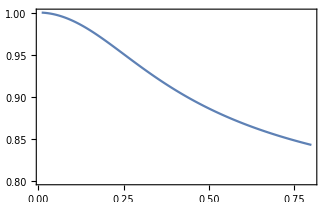

```mathematica
ListLinePlot[testtable1,
PlotRange->{All,{0.8,1}}]
```

```mathematica
PrettyTiming[testtable1ana=Table[{ΩΩ,Chop[ℱanalytical/.t-> π/(2 λ Ω)/.idealParameters/.Ω->ΩΩ//N]},{ΩΩ,10^-2,0.8,10^-3}];]
```

0h : 0m : 1s

Just comparing the numerical with the analytical formula. They must match, otherwise something is wrong with the analytical.

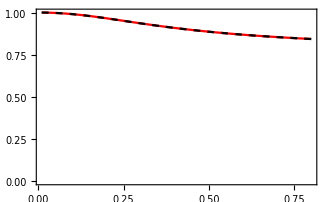

```mathematica
ListLinePlot[{testtable1,testtable1ana},
PlotStyle->{Red,{Dashed,Black}},
PlotRange->{All,{0,1}}]
```

Cool. Now I want to plot the fidelity between the target state and the real state at time  t = π/(2 λ Ω)  as a function of the ratio, λ, and the Larmor frequency in the excited state Ω for a time.

```mathematica
PrettyTiming[idealsituationℱcontourplot=Table[{ΩΩ,λλ,Chop[ℱanalytical/.t-> π/(2 λ Ω)/.λ->λλ/.idealParameters/.Ω->ΩΩ//N]},{λλ,0.5,3,10^-1},{ΩΩ,10^-2,0.8,10^-3}];]
```

0h : 0m : 11s

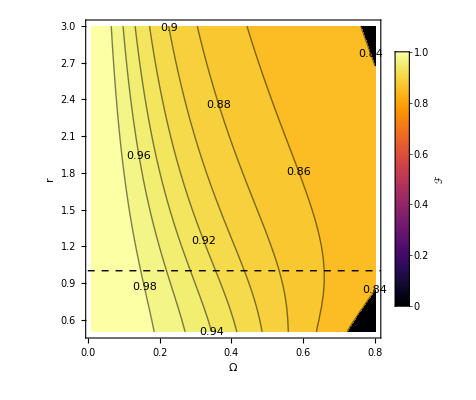

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf},

cf= MPLColorMap["Inferno"];

fidelityIdealMagneticFieldContourplot=ListContourPlot[Flatten[idealsituationℱcontourplot,1],PlotRange->All,FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->20,Black],Style["r",FontFamily->"Times",FontSize->20,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->20,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->20,Black]],Right],Epilog->{{Black,Dashed,Line[{{0,1},{1,1}}]}}]

]
```

```mathematica
Export[PlotsPath<>"fidelityIdealMagneticFieldContourplot.pdf",fidelityIdealMagneticFieldContourplot];
Export[PlotsPath<>"fidelityIdealMagneticFieldContourplot.svg",fidelityIdealMagneticFieldContourplot];
```

The contour plot above is obtained considering the ideal situation where the magnetic field for both, electron and hole, points only in the x-direction (nx,ny,nz)=(1,0,0). The decay rate is set to γ=1 and it is computed at the time we expect it to reach the target state t=π/(2 λ Ω).

As expected by intuition, when the Ω<<γ=1 the fidelity is close to unity, almost independent of the ratio r is close to unity we have higher fidelity in the region . Overall the fidelity in the situation where the only imperfection is the difference between the larmor frequencies is high. It decreases as Ω approach γ, as expected.

Below, I plot the fidelity in the very ideal situation where r=1, highlighted by the dashed black line in the contour plot.

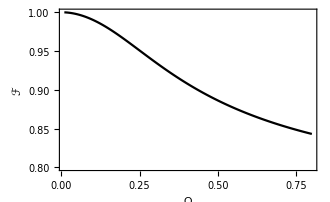

```mathematica
idealFidelity =ListLinePlot[testtable1ana,
FrameLabel->{"Ω","ℱ"},
PlotStyle->{{Black}},
PlotRange->{All,{0.8,1}}]
Export[PlotsPath<>"idealFidelity.pdf",idealFidelity];
Export[PlotsPath<>"idealFidelity.svg",idealFidelity];
```

Next step is to consider an anysotropic magnetic field (nx,ny,nz). We set the ratio as λ={1,1.5,2.5}.

Below I turn on only the component y of the magnetic field

```mathematica
Tablepar1=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar2=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1.5/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar3=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->2.5/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

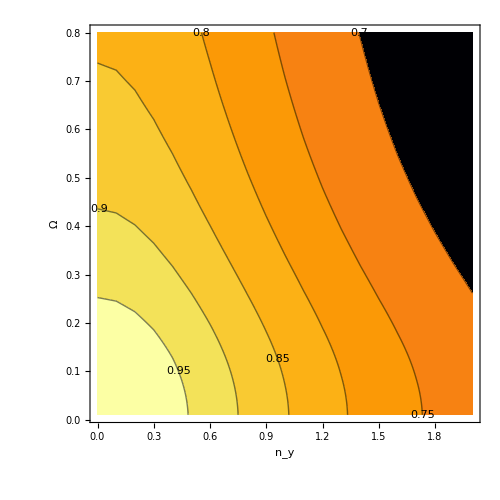
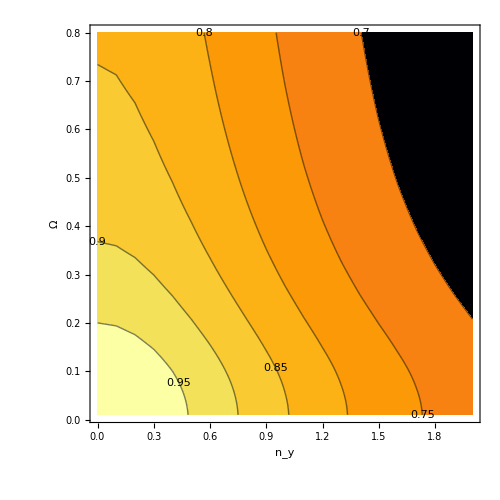
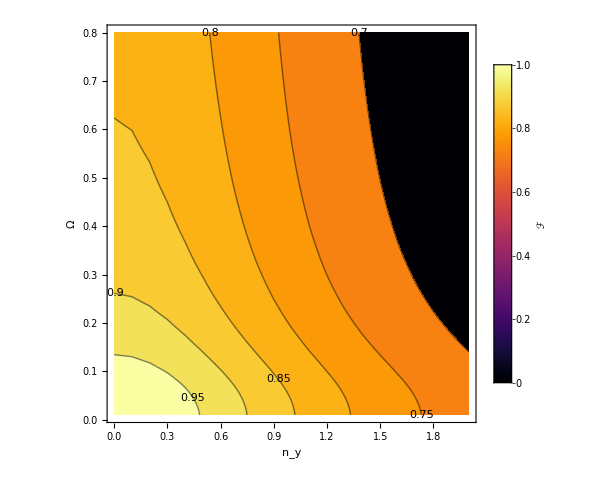
-Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf,plotSize,frameLabelStyle},cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->20,FontColor->Black,FontFamily->"Times"};
FidelityContourplot1=Grid[{{
ListContourPlot[Flatten[N@Tablepar1,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar2,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar3,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},
LegendLabel->Style["ℱ",FontSize->20,FontFamily->"Times"]],Right],

ImageSize->plotSize]}}]]
Export[PlotsPath<>"FidelityContourplot1asfunctionofny.pdf",FidelityContourplot1];
Export[PlotsPath<>"FidelityContourplot1asfunctionofny.svg",FidelityContourplot1];
```

Now I turn on only the component z of the magnetic field.

```mathematica
Tablepar1z=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1/.{nx->N[Normalize@{1,0,nny}][[1]],ny->N[Normalize@{1,0,nny}][[2]],nz->N[Normalize@{1,0,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar2z=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1.5/.{nx->N[Normalize@{1,0,nny}][[1]],ny->N[Normalize@{1,0,nny}][[2]],nz->N[Normalize@{1,0,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar3z=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->2.5/.{nx->N[Normalize@{1,0,nny}][[1]],ny->N[Normalize@{1,0,nny}][[2]],nz->N[Normalize@{1,0,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf,plotSize,frameLabelStyle},cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->20,FontColor->Black,FontFamily->"Times"};
FidelityContourplot2z=Grid[{{
ListContourPlot[Flatten[N@Tablepar1z,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar2z,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar3z,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},
LegendLabel->Style["ℱ",FontSize->20,FontFamily->"Times"]],Right],

ImageSize->plotSize]}}]]
Export[PlotsPath<>"FidelityContourplot1asfunctionofnz.pdf",FidelityContourplot2z];
Export[PlotsPath<>"FidelityContourplot1asfunctionofnz.svg",FidelityContourplot2z];
```

-Graphics- | -Graphics- | -Graphics-

Finally, I turn on both components with the same strength.

```mathematica
Tablepar1yz=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar2yz=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->1.5/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
Tablepar3yz=Table[{nny,ΩΩ,(ℱanalytical/.γ->1/.t-> π/(2 λ Ω)/.λ->2.5/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf,plotSize,frameLabelStyle},cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->20,FontColor->Black,FontFamily->"Times"};
FidelityContourplot3yz=Grid[{{
ListContourPlot[Flatten[N@Tablepar1yz,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar2yz,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@Tablepar3yz,1],
PlotRange->All,
FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(y\)]\)",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},
LegendLabel->Style["ℱ",FontSize->20,FontFamily->"Times"]],Right],

ImageSize->plotSize]}}]]
Export[PlotsPath<>"FidelityContourplot1asfunctionofnynz.pdf",FidelityContourplot3yz];
Export[PlotsPath<>"FidelityContourplot1asfunctionofnynz.svg",FidelityContourplot3yz];
```

-Graphics- | -Graphics- | -Graphics-

#### Getting rid of the powers of Ω

```mathematica
ℱanalytical//cf
```

(ⅇ^(-t (γ+ⅈ λ Ω)) (ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

Let’s take out by hand the powers of Ω:

```mathematica
ℱanalyticalsimplified=ℱanalytical//Expand
```

-γ^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^3 λ^2 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^3 λ^2 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^3 λ^3 Ω^3)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 γ^2 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^2 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^2 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^2 λ Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^2 λ Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^2 λ^2 Ω^4)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^2 λ^2 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(γ^2 λ^4 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^2 λ^4 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^2 λ^4 Ω^4)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^2 λ^4 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^2 λ^4 Ω^4)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) nx γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ λ Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ λ^2 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ λ^2 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ λ^3 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ λ^4 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ λ^4 Ω^5)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-Ω^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) Ω^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(λ^2 Ω^6)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) λ^2 Ω^6)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(λ^4 Ω^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) λ^4 Ω^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

Keeping only the terms linear in Ω and simplifying:

```mathematica
ℱsimplified=-γ^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf
```

(ⅇ^(-t (γ+ⅈ λ Ω)) γ^5 (-2 ⅇ^(t (γ+ⅈ λ Ω)) γ-2 ⅇ^(2 t γ+ⅈ t λ Ω) (-1+ny nz) γ+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) nx λ Ω+ⅇ^(t (γ+ⅈ (1+λ) Ω)) nx λ Ω+ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) (γ-ⅈ λ Ω)+ⅇ^(2 t γ) (ⅈ nx+ny nz) (γ+ⅈ λ Ω)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
ℱsimplified2 = -γ^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf
```

(ⅇ^(-t (γ+ⅈ λ Ω)) γ^4 (ⅇ^(t (γ+ⅈ (-1+λ) Ω)) λ Ω (nx (γ-2 ⅈ Ω)+ny nz λ Ω)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) λ Ω (nx (γ+2 ⅈ Ω)+ny nz λ Ω)+ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) (γ^2-ⅈ γ λ Ω+(2+λ^2) Ω^2)+ⅇ^(2 t γ) (ⅈ nx+ny nz) (γ^2+ⅈ γ λ Ω+(2+λ^2) Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+(3+2 λ^2) Ω^2)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2+(-3-2 λ^2+2 ny nz (1+λ^2)) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

SImplifying further (‘neglecting the Ω^4 and Ω^2 in the denominator):

```mathematica
ℱsimplified=(ⅇ^(-t (γ+ⅈ λ Ω)) γ^5 (-2 ⅇ^(t (γ+ⅈ λ Ω)) γ-2 ⅇ^(2 t γ+ⅈ t λ Ω) (-1+ny nz) γ+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) nx λ Ω+ⅇ^(t (γ+ⅈ (1+λ) Ω)) nx λ Ω+ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) (γ-ⅈ λ Ω)+ⅇ^(2 t γ) (ⅈ nx+ny nz) (γ+ⅈ λ Ω)))/(4 (-1+ⅇ^(t γ)) (γ^2) (γ^4))//cf
```

1/(4 (-1+ⅇ^(t γ)) γ)ⅇ^(-t (γ+ⅈ λ Ω)) (-2 ⅇ^(t (γ+ⅈ λ Ω)) γ-2 ⅇ^(2 t γ+ⅈ t λ Ω) (-1+ny nz) γ+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) nx λ Ω+ⅇ^(t (γ+ⅈ (1+λ) Ω)) nx λ Ω+ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) (γ-ⅈ λ Ω)+ⅇ^(2 t γ) (ⅈ nx+ny nz) (γ+ⅈ λ Ω))

```mathematica
ℱsimplified//Expand
```

-1/(2 (-1+ⅇ^(t γ)))+ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω))/(2 (-1+ⅇ^(t γ)))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx)/(4 (-1+ⅇ^(t γ)))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx)/(4 (-1+ⅇ^(t γ)))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz)/(4 (-1+ⅇ^(t γ)))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz)/(4 (-1+ⅇ^(t γ)))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz)/(2 (-1+ⅇ^(t γ)))-(ⅇ^(t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz λ Ω)/(4 (-1+ⅇ^(t γ)) γ)

```mathematica
independentofn = -1/(2 (-1+ⅇ^(t γ)))+ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω))/(2 (-1+ⅇ^(t γ)))//cf
dependentofnx =1/nx(-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx)/(4 (-1+ⅇ^(t γ)))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx)/(4 (-1+ⅇ^(t γ))) -(ⅇ^(t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx λ Ω)/(4 (-1+ⅇ^(t γ)) γ))//cf
dependentofnynz=1/(ny nz)((ⅇ^(t (γ+ⅈ λ Ω)) ny nz)/(4 (-1+ⅇ^(t γ)))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz)/(4 (-1+ⅇ^(t γ)))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz)/(2 (-1+ⅇ^(t γ)))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz λ Ω)/(4 (-1+ⅇ^(t γ)) γ)+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz λ Ω)/(4 (-1+ⅇ^(t γ)) γ))//cf
```

1/2

(ⅇ^(-t (γ+ⅈ λ Ω)) (ⅇ^(t (γ+ⅈ (-1+λ) Ω)) λ Ω+ⅇ^(t (γ+ⅈ (1+λ) Ω)) λ Ω+ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ γ-λ Ω)+ⅈ ⅇ^(2 t γ) (γ+ⅈ λ Ω)))/(4 (-1+ⅇ^(t γ)) γ)

(ⅇ^(t γ) (γ (-1+Cos[t λ Ω])+λ Ω Sin[t λ Ω]))/(2 (-1+ⅇ^(t γ)) γ)

```mathematica
confirmingitsok = ℱsimplified - (1/2+nx dependentofnx +ny nz dependentofnynz )//cf
```

0

```mathematica
ℱsimplified2//Expand
```

-γ^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
independentofn =-γ^6/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(3 γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(3 ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf
dependentofnx =1/nx(-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) nx γ^4 λ Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) nx γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))//cf
dependentofnynz=1/(ny nz)(+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^6)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^6)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅈ ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^5 λ Ω)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/(2 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(2 t γ-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅇ^(2 t γ+ⅈ t λ Ω-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/((-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(t (γ+ⅈ (-1+λ) Ω)-t (γ+ⅈ λ Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-t (γ+ⅈ λ Ω)+t (γ+ⅈ (1+λ) Ω)) ny nz γ^4 λ^2 Ω^2)/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))//cf
```

(γ^4 (γ^2+(3+2 λ^2) Ω^2))/(2 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

(ⅇ^(-t (γ+ⅈ λ Ω)) γ^4 (ⅇ^(t (γ+ⅈ (-1+λ) Ω)) λ (γ-2 ⅈ Ω) Ω+ⅇ^(t (γ+ⅈ (1+λ) Ω)) λ (γ+2 ⅈ Ω) Ω-ⅈ ⅇ^(2 t (γ+ⅈ λ Ω)) (γ^2-ⅈ γ λ Ω+(2+λ^2) Ω^2)+ⅈ ⅇ^(2 t γ) (γ^2+ⅈ γ λ Ω+(2+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

(ⅇ^(-t (γ+ⅈ λ Ω)) γ^4 (ⅇ^(t (γ+ⅈ (-1+λ) Ω)) λ^2 Ω^2+ⅇ^(t (γ+ⅈ (1+λ) Ω)) λ^2 Ω^2-2 ⅇ^(2 t γ+ⅈ t λ Ω) (γ^2+2 (1+λ^2) Ω^2)+ⅇ^(2 t (γ+ⅈ λ Ω)) (γ^2-ⅈ γ λ Ω+(2+λ^2) Ω^2)+ⅇ^(2 t γ) (γ^2+ⅈ γ λ Ω+(2+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
confirmingitsok = ℱsimplified2 - (independentofn+nx dependentofnx +ny nz dependentofnynz )//cf
```

0

```mathematica
Plot[ℱsimplified2/.idealParameters//cf,{Ω,0.1,1}]
```

$Aborted

### 5) Plotting the Bloch sphere - Working here

All of this is absolutely cool to visualize the dynamics of the states in the Bloch/ Poincaré spheres, but not very quantitative. In the next part I plot the fidelity.

```mathematica
PoincareSphere[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["R"],{0,0,1.2}],Text[texKet["L"],{0,0,-1.2}],Text[texKet["H"],{1.2,0,0}],Text[texKet["V"],{-1.2,0,0}],Text[texKet["A"],{0,1.2,0}],Text[texKet["D"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
PoicareSphere[]
```

-Graphics3D-

```mathematica
BlochSphereSpin[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["↑"],{0,0,1.2}],Text[texKet["↓"],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["i"],{0,1.2,0}],Text[texKet["-i"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
BlochSphereSpin[]
```

-Graphics3D-

To Plot the Bloch sphere it suffices to compute the bloch vectors:

```mathematica
expectationvaluesxUp=Tr[σx.ρspt2];
expectationvaluesyUp=Tr[σy.ρspt2];
expectationvalueszUp=Tr[σz.ρspt2];

(*Bloch vector of the spin initially in the up state*)
blochvectorspinUp={expectationvaluesx,expectationvaluesy,expectationvaluesz};

(*Poincaré vector for spin up and down*)
poincarevectorUp={0,-1/2 Sin[Ωe t],Cos[Ωe t]};
poincarevectorDw={0,1/2 Sin[Ωe t],-Cos[Ωe t]};

(*Parameters for the plots*)
parsphere1={ny->0,nx->1,nz->0,Ωg->Ω,Ωe->Ω,γ->1};
parsphere2={ny->0.3/1.0862780491200215,nx->1/1.0862780491200215,nz->0.3/1.0862780491200215,Ωg->Ω,Ωe->Ω,γ->1};
parsphere3={ny->0,nx->1,nz->0,Ωg->2.4Ω,Ωe->Ω,γ->1};
parsphere4={ny->0.3/1.0862780491200215,nx->1/1.0862780491200215,nz->0.3/1.0862780491200215,Ωg->2.4Ω,Ωe->Ω,γ->1};
```

```mathematica
(*Bloch vectors for the spin up*)
blochvectorsphere1Up=blochvectorspinUp/.parsphere1;
blochvectorsphere2Up=blochvectorspinUp/.parsphere2;
blochvectorsphere3Up=blochvectorspinUp/.parsphere3;
blochvectorsphere4Up=blochvectorspinUp/.parsphere4;
(*Poincaré vectors for the spin up*)
poincarevectorsphere1Up=poincarevectorUp/.parsphere1;
poincarevectorsphere2Up=poincarevectorUp/.parsphere2;
poincarevectorsphere3Up=poincarevectorUp/.parsphere3;
poincarevectorsphere4Up=poincarevectorUp/.parsphere4;
(*Poincaré vectors for the spin dw*)
poincarevectorsphere1Dw=poincarevectorDw/.parsphere1;
poincarevectorsphere2Dw=poincarevectorDw/.parsphere2;
poincarevectorsphere3Dw=poincarevectorDw/.parsphere3;
poincarevectorsphere4Dw=poincarevectorDw/.parsphere4;
```

```mathematica
sphere1Up=Grid[{Table[Show[BlochSphereSpin[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[blochvectorsphere1Up/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[blochvectorsphere1Up/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|⟨s⟩|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"Sphere1UpSE.pdf",sphere1];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
sphere2Up=Grid[{Table[Show[BlochSphereSpin[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Chop[Table[blochvectorsphere2Up/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[blochvectorsphere2Up/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|⟨s⟩|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"Sphere2UpSE.pdf",sphere2Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
sphere3Up=Grid[{Table[Show[BlochSphereSpin[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[blochvectorsphere3Up/.Ω->ΩΩ,{t,0,π/(2(2.4 ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[blochvectorsphere3Up/.Ω->ΩΩ],{t,0,π/(2 (2.4 ΩΩ))}],FrameLabel->{"γt","|⟨s⟩|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"Sphere3UpSE.pdf",sphere3Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
sphere4Up=Grid[{Table[Show[BlochSphereSpin[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[blochvectorsphere4Up/.Ω->ΩΩ,{t,0,π/(2 (2.4 ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[blochvectorsphere4Up/.Ω->ΩΩ],{t,0,π/(2 (2.4 ΩΩ))}],FrameLabel->{"γt","|⟨s⟩|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"Sphere4UpSE.pdf",sphere4Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere1Up=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere1Up/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere1Up/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere1UpSE.pdf",psphere1Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere2Up=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere2Up/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere2Up/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere2UpSE.pdf",psphere2Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere3Up=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere3Up/.Ω->ΩΩ,{t,0,π/(2 (2.4ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere3Up/.Ω->ΩΩ],{t,0,π/(2 (2.4ΩΩ))}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere3UpSE.pdf",psphere3Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere4Up=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere4Up/.Ω->ΩΩ,{t,0,π/(2 (2.4ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere4Up/.Ω->ΩΩ],{t,0,π/(2 (2.4ΩΩ))}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere4UpSE.pdf",psphere4Up];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere1Dw=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere1Dw/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere1Dw/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere1DwSE.pdf",psphere1Dw];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere2Dw=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere2Dw/.Ω->ΩΩ,{t,0,π/(2 ΩΩ)}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere2Dw/.Ω->ΩΩ],{t,0,π/(2 ΩΩ)}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere2DwSE.pdf",psphere2Dw];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere3Dw=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere3Dw/.Ω->ΩΩ,{t,0,π/(2 (2.4ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere3Dw/.Ω->ΩΩ],{t,0,π/(2 (2.4ΩΩ))}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere3DwSE.pdf",psphere3Dw];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

```mathematica
psphere4Dw=Grid[{Table[Show[PoincareSphere[],Graphics3D[{Black,Thickness[Medium],Arrow[Chop[Table[poincarevectorsphere4Dw/.Ω->ΩΩ,{t,0,π/(2 (2.4ΩΩ))}]]]}]],{ΩΩ,{1/10^2,1/10,2/10}}],Table[ListLinePlot[Table[Norm[poincarevectorsphere4Dw/.Ω->ΩΩ],{t,0,π/(2 (2.4ΩΩ))}],FrameLabel->{"γt","|𝓅|"}],{ΩΩ,{1/10^2,1/10,2/10}}]}]
Export[PlotsPath<>"PoincareSphere4DwSE.pdf",psphere4Dw];
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics-

Now I write the arbitrary spin rotation rotation operator as given by Eq 4.12 of Nielsen & Chuang - Quantum computation and quantum information, and the dagger with the cf command to consider the parameters α,β and δ real. These are the parameters that I’ll maximize over to find the repeatbility:

```mathematica
USp=cf[{{Exp[ⅈ (α-β/2-δ/2)] Cos[ζ/2],-Exp[ⅈ (α-β/2+δ/2)] Sin[ζ/2]},{Exp[ⅈ (α+β/2-δ/2)] Sin[ζ/2],Exp[ⅈ (α+β/2+δ/2)] Cos[ζ/2]}}];
USpDag=mf[cf[ConjugateTranspose[USp]]];
```

(ⅇ^(-1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] | ⅇ^(-1/2 ⅈ (2 α+β-δ)) Sin[ζ/2]
-ⅇ^(-1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] | ⅇ^(-1/2 ⅈ (2 α+β+δ)) Cos[ζ/2])

Sanity check: is it really unitary? (This type of check is silly but can spot some stupid typos, since I have 4 parameters, a wrong sign can screw up everything to come)

```mathematica
mf[cf[USp.USpDag]];
```

(1 | 0
0 | 1)

Good, since I have a valid density matrix and a unitary I can safely rotate it and ask for the eigenvalues.

Finally, the spin density matrix rotated in time, and its Eigenvalues are:

```mathematica
ρspRotated=mf[USp.ρspt.USpDag];
EigenvaluesρspRotated=Eigenvalues[ρspRotated]
```

(ⅇ^(-1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (-ⅇ^(1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (-(ⅇ^(-t (γ-ⅈ Ωg)) (nx+ⅈ ny) (ⅇ^(t γ) (1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t (γ-2 ⅈ Ωg)) (-1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(-ⅈ t Ωg) Ωg (ⅈ γ+nz Ωg)-2 ⅇ^(t (γ-ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[t Ωe])/(4 (γ^2+Ωg^2))-1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (ⅇ^(-t γ) Cos[(t Ωe)/2]^2+γ (-((nx^2+ny^2) ((-2+ⅇ^(-ⅈ t Ωg)+ⅇ^(ⅈ t Ωg)) γ^2-ⅈ ⅇ^(-ⅈ t Ωg) (-1+ⅇ^(2 ⅈ t Ωg)) γ Ωg+2 (-1+ⅇ^(-t γ)) Ωg^2) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+1/2 Cos[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2)))))-ⅇ^(-1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (ⅇ^(1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (γ (-(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2)))+1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])-ⅇ^(1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (ⅇ^(-t γ) Sin[(t Ωe)/2]^2+γ (((nx^2+ny^2) Cos[(t Ωe)/2]^2 (γ^2+Ωg^2-ⅇ^(-t γ) Ωg^2-γ^2 Cos[t Ωg]-γ Ωg Sin[t Ωg]))/(2 γ^3+2 γ Ωg^2)+1/2 Sin[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2))))) | ⅇ^(-1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (-ⅇ^(1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (-(ⅇ^(-t (γ-ⅈ Ωg)) (nx+ⅈ ny) (ⅇ^(t γ) (1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t (γ-2 ⅈ Ωg)) (-1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(-ⅈ t Ωg) Ωg (ⅈ γ+nz Ωg)-2 ⅇ^(t (γ-ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[t Ωe])/(4 (γ^2+Ωg^2))-1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (ⅇ^(-t γ) Cos[(t Ωe)/2]^2+γ (-((nx^2+ny^2) ((-2+ⅇ^(-ⅈ t Ωg)+ⅇ^(ⅈ t Ωg)) γ^2-ⅈ ⅇ^(-ⅈ t Ωg) (-1+ⅇ^(2 ⅈ t Ωg)) γ Ωg+2 (-1+ⅇ^(-t γ)) Ωg^2) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+1/2 Cos[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2)))))+ⅇ^(-1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (ⅇ^(1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (γ (-(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2)))+1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])-ⅇ^(1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (ⅇ^(-t γ) Sin[(t Ωe)/2]^2+γ (((nx^2+ny^2) Cos[(t Ωe)/2]^2 (γ^2+Ωg^2-ⅇ^(-t γ) Ωg^2-γ^2 Cos[t Ωg]-γ Ωg Sin[t Ωg]))/(2 γ^3+2 γ Ωg^2)+1/2 Sin[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2)))))
ⅇ^(-1/2 ⅈ (2 α-β-δ)) Cos[ζ/2] (ⅇ^(1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (-(ⅇ^(-t (γ-ⅈ Ωg)) (nx+ⅈ ny) (ⅇ^(t γ) (1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t (γ-2 ⅈ Ωg)) (-1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(-ⅈ t Ωg) Ωg (ⅈ γ+nz Ωg)-2 ⅇ^(t (γ-ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[t Ωe])/(4 (γ^2+Ωg^2))-1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (ⅇ^(-t γ) Cos[(t Ωe)/2]^2+γ (-((nx^2+ny^2) ((-2+ⅇ^(-ⅈ t Ωg)+ⅇ^(ⅈ t Ωg)) γ^2-ⅈ ⅇ^(-ⅈ t Ωg) (-1+ⅇ^(2 ⅈ t Ωg)) γ Ωg+2 (-1+ⅇ^(-t γ)) Ωg^2) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+1/2 Cos[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2)))))-ⅇ^(-1/2 ⅈ (2 α-β+δ)) Sin[ζ/2] (ⅇ^(1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (γ (-(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2)))+1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (ⅇ^(-t γ) Sin[(t Ωe)/2]^2+γ (((nx^2+ny^2) Cos[(t Ωe)/2]^2 (γ^2+Ωg^2-ⅇ^(-t γ) Ωg^2-γ^2 Cos[t Ωg]-γ Ωg Sin[t Ωg]))/(2 γ^3+2 γ Ωg^2)+1/2 Sin[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2))))) | ⅇ^(-1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (ⅇ^(1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (-(ⅇ^(-t (γ-ⅈ Ωg)) (nx+ⅈ ny) (ⅇ^(t γ) (1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t (γ-2 ⅈ Ωg)) (-1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(-ⅈ t Ωg) Ωg (ⅈ γ+nz Ωg)-2 ⅇ^(t (γ-ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[t Ωe])/(4 (γ^2+Ωg^2))-1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (ⅇ^(-t γ) Cos[(t Ωe)/2]^2+γ (-((nx^2+ny^2) ((-2+ⅇ^(-ⅈ t Ωg)+ⅇ^(ⅈ t Ωg)) γ^2-ⅈ ⅇ^(-ⅈ t Ωg) (-1+ⅇ^(2 ⅈ t Ωg)) γ Ωg+2 (-1+ⅇ^(-t γ)) Ωg^2) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+1/2 Cos[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2)))))+ⅇ^(-1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (ⅇ^(1/2 ⅈ (2 α+β-δ)) Sin[ζ/2] (γ (-(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2)))+1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe])+ⅇ^(1/2 ⅈ (2 α+β+δ)) Cos[ζ/2] (ⅇ^(-t γ) Sin[(t Ωe)/2]^2+γ (((nx^2+ny^2) Cos[(t Ωe)/2]^2 (γ^2+Ωg^2-ⅇ^(-t γ) Ωg^2-γ^2 Cos[t Ωg]-γ Ωg Sin[t Ωg]))/(2 γ^3+2 γ Ωg^2)+1/2 Sin[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2))))))

If[25790092725221331101===$SessionID,%141,Message[Syntax::noinfoker];Missing[NotAvailable];]

Sanity check: Is the rotated density matrix a valid one? (Always good to double check before going to the heavy computations)

```mathematica
Simplify[Tr[ρspRotated]-1]
```

0

### 6) Repeatability and reversability ☑

In this section I use the analytical density matrix computed in sec.  to:
	1) Obtain the repeatability ℛ_↑=ℱ(ρsp, ρ^↑) numerically;
	2) Compare it with the (g^2)_RL(t) data and the P_↑;

Main results:
	* The probability of the spin being in the state Up and the Repeatability match perfectly, also we can look at the probability of being up and in the ground state, which match after ~6γ which is expected, meaning that there is not emission from the excited state taking place anymore.
	* The minima and maxima of the “correctability” match the minima and maxima of the repeatability, having a maxima for every point of minima/maxima.

#### Computing the reversibility

```mathematica
ρspt = ({{ℴUpUp, ℴDwUp}, {ℴUpDw, ℴDwDw}})//mf;
ρUp = ({{1, 0}, {0, 0}});
```

(ⅇ^(-t γ) Cos[(t Ωe)/2]^2+γ (-((1-nz^2) ((-2+ⅇ^(-ⅈ t Ωg)+ⅇ^(ⅈ t Ωg)) γ^2-ⅈ ⅇ^(-ⅈ t Ωg) (-1+ⅇ^(2 ⅈ t Ωg)) γ Ωg+2 (-1+ⅇ^(-t γ)) Ωg^2) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+1/2 Cos[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2))) | γ (-(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2))+(ⅇ^(-t (γ+ⅈ Ωg)) (nx-ⅈ ny) (ⅇ^(t (γ+2 ⅈ Ωg)) (-1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t γ) (1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(ⅈ t Ωg) Ωg (-ⅈ γ+nz Ωg)-2 ⅇ^(t (γ+ⅈ Ωg)) nz (γ^2+Ωg^2)) Sin[(t Ωe)/2]^2)/(4 γ (γ^2+Ωg^2)))+1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe]
-(ⅇ^(-t (γ-ⅈ Ωg)) (nx+ⅈ ny) (ⅇ^(t γ) (1+nz) γ (γ-ⅈ Ωg)+ⅇ^(t (γ-2 ⅈ Ωg)) (-1+nz) γ (γ+ⅈ Ωg)+2 ⅇ^(-ⅈ t Ωg) Ωg (ⅈ γ+nz Ωg)-2 ⅇ^(t (γ-ⅈ Ωg)) nz (γ^2+Ωg^2)) Cos[t Ωe])/(4 (γ^2+Ωg^2))-1/2 ⅈ ⅇ^(-t γ) Sin[t Ωe] | ⅇ^(-t γ) Sin[(t Ωe)/2]^2+γ (((1-nz^2) Cos[(t Ωe)/2]^2 (γ^2+Ωg^2-ⅇ^(-t γ) Ωg^2-γ^2 Cos[t Ωg]-γ Ωg Sin[t Ωg]))/(2 γ^3+2 γ Ωg^2)+1/2 Sin[(t Ωe)/2]^2 ((1+nz^2)/γ-(ⅇ^(-t γ) (2 γ^2+Ωg^2+nz^2 Ωg^2))/(γ^3+γ Ωg^2)-((-1+nz^2) (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/(γ^2+Ωg^2))))

```mathematica
Eigenvaluesρsp=Eigenvalues[ρspt]
```

{(ⅇ^(-t γ-111-ⅈ t Ωg) (1-1))/(16 (γ^2+Ωg^2)),(ⅇ^1 (1))/(16 (γ^2+Ωg^2))}
 |  |  |  |

```mathematica
Eigenvaluesρsp=Eigenvaluesρsp/.nx^2+ny^2->1-nz^2
```

{(ⅇ^(-t γ-111-ⅈ t Ωg) (1-1))/(16 (γ^2+Ωg^2)),(ⅇ^1 (1))/(16 (γ^2+Ωg^2))}
 |  |  |  |

```mathematica
(*I always like to keep track on how much time it takes to perform the full simulation, if it's longer than 5 minutes it's worthy of receiving a DumpSave*)
Clear[ℛUpoftList,FirstEigenvalueOft,SecondEigenvalueOft];
PrettyTiming[

Module[{value1,value2,PickThisOne,TheMinimumIs},

Do[
(*For each set of physical parameters of te g2 I start a list that has all the physical parameters as a label. This will be initialized for every set in the list physicalparameterslistg2 (The outer Do=while of python)*)
ℛUpoftList[physicalparameters]={};
MinimumEigenvalueoftList[physicalparameters]={};
FirstEigenvalueOft[physicalparameters]={};
SecondEigenvalueOft[physicalparameters]={};
PrintTemporary["Out"];
(*Then the internal Do will update the above lists.*)
Do[
(*It maximizes numerically the eigenvalues with respect to α,β,δ and ζ,for the physical parameters. The Magnetic field direction is fixed (no chaos for now)*)
value1=Eigenvaluesρsp[[1]]/.physicalparameters/.MagneticFieldDirection/.t->x;(*Quiet@NMaximize[Re[Chop@EigenvaluesρspRotated⟦1⟧/.physicalparameters/.MagneticFieldDirection/.t->x],{α,β,δ,ζ}]⟦1⟧;*)
value2=Eigenvaluesρsp[[2]]/.physicalparameters/.MagneticFieldDirection/.t->x;(*Quiet@NMaximize[Re[Chop@EigenvaluesρspRotated⟦2⟧/.physicalparameters/.MagneticFieldDirection/.t->x],{α,β,δ,ζ}]⟦1⟧;
*)
(*Then I pick the maximum value of the Eigenvalues at this point of time:*)
PickThisOne=Max[Re@Chop@value1,Re@Chop@value2];
(*I'll take the minimum as well because I think this guy might give some info:*)
TheMinimumIs = Min[Re@Chop@value1,Re@Chop@value2];
(*PrintTemporary[PickThisOne];*)
(*Finally, I update the list. the first one is the repeatability as a function of time, and since it costs nothing I'm also keeping track of both Eigenvalues*)
ℛUpoftList[physicalparameters]=AppendTo[ℛUpoftList[physicalparameters],{x,PickThisOne}];
MinimumEigenvalueoftList[physicalparameters]=AppendTo[MinimumEigenvalueoftList[physicalparameters],{x,TheMinimumIs}];
FirstEigenvalueOft[physicalparameters]=AppendTo[FirstEigenvalueOft[physicalparameters],{x,value1}];
SecondEigenvalueOft[physicalparameters]=AppendTo[SecondEigenvalueOft[physicalparameters],{x,value2}];

,{x,0,40,0.5}],

{physicalparameters, physicalparameterslistg2}]

]]
```

0h : 0m : 11s

#### Computing repeatability numerically and plot

```mathematica
Do[repeatabilty[k]=Table[{x,Chop@QuantumFidelity[ρspt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x,ρUp]},{x,0,40,0.1}]
,{k,1,Length@physicalparameterslistg2}]
```

```mathematica
ρspt/.t->7.66/.physicalparameterslistg2[[6]]/.MagneticFieldDirection//mf;
```

(0.14002 | 0.+0.0216497 ⅈ
0.-0.0216497 ⅈ | 0.85998)

```mathematica
Chop@Tr[ρspt/.t->7.66/.physicalparameterslistg2[[6]]/.MagneticFieldDirection]
```

1.

```mathematica
Chop@PUpt/.t->7.66/.physicalparameterslistg2[[6]]/.MagneticFieldDirection
```

0.14002

### a: Plot of repeatability and reversability ☑

```mathematica
Fig9RepeatabilityAndPUp= 

Module[{tf},
tf=40;
Grid[{
Table[
ListLinePlot[
{repeatabilty[k],Table[{x,PUpt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}],Table[{x,PUpgt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}],ℛUpoftList[physicalparameterslistg2[[k]]],Table[{x,PUpgt+PDwgt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}]},
PlotRange->{All,{-0.1,1.2}},
PlotLegends->If[k==1,legend[{"ℛ_↑","P(↑)","P(↑|g)","max Eigval","P_g"},{0.,0.4}, LegendLayout->"Row"],None],
Epilog->Inset[alphabetlabel[[k]],{2,1.1}],
FrameLabel->{"γt",""},
PlotStyle->{Green,{Black,Dashed},{Red,Dotted},{Purple}, {Orange}}],

{k,1,Length@physicalparameterslistg2/2}],

Table[
ListLinePlot[
{repeatabilty[k],Table[{x,PUpt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}],Table[{x,PUpgt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}],ℛUpoftList[physicalparameterslistg2[[k]]],Table[{x,PUpgt+PDwgt/.physicalparameterslistg2[[k]]/.MagneticFieldDirection/.t->x},{x,0,tf,0.1}]},
PlotRange->{All,{-0.1,1.2}},
Epilog->Inset[alphabetlabel[[k]],{2,1.1}],
FrameLabel->{"γt",""},
PlotStyle->{Green,{Black,Dashed},{Red,Dotted},{Purple}, {Orange}}],

{k,Length@physicalparameterslistg2/2+1,Length@physicalparameterslistg2}]
}]
]
Export[PlotsPath<>"Fig9-RepeatabilityAndPUp.pdf",Fig9RepeatabilityAndPUp];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Discussion: We observe that the probability of the spin being in the state Up and the Repeatability match perfectly, also we can look at the probability of being up and in the ground state, which match after ~6γ which is expected, meaning that there is not emission from the excited state taking place anymore.

## 2. Maria’s fidelity of the spin at the moment of re-excitation

```mathematica
ℱbruno=ℱanalytical/.t->π/(2 λ Ω)//cf
```

-((ⅈ ⅇ^(-(π γ)/(2 λ Ω)) (ⅇ^((π (γ-ⅈ Ω))/(2 λ Ω)) γ λ Ω (ⅈ γ+Ω) (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)-2 ⅈ ⅇ^((π γ)/(2 λ Ω)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)+2 ⅈ ⅇ^((π γ)/(λ Ω)) ((1+nx-ny nz) γ^6+ny nz γ^5 λ Ω+γ^4 (3+2 λ^2-2 ny nz (1+λ^2)+nx (2+λ^2)) Ω^2+ny nz γ^3 λ^3 Ω^3+γ^2 (3+λ^4-ny nz (-1+λ^2)^2+nx (1+λ^2)) Ω^4+ny nz γ λ (-1+λ^2) Ω^5+(-1+λ^2)^2 Ω^6)+ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2) (ⅈ ny nz λ Ω+nx (ⅈ γ+Ω))))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

Let’s collect the terms proportional to nx and ny nz:

```mathematica
groupedExpression=Collect[ℱbruno,{nx,ny},Simplify];

constantTerms=groupedExpression[[1]];
groupedExpression=Rest[groupedExpression];
```

```mathematica
constantTerms
```

1/2

```mathematica
groupedExpression
```

(ⅇ^(-(ⅈ π)/(2 λ)) nx γ (λ Ω (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((ⅈ π)/λ) λ Ω (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)+2 ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) γ (γ^2+(1+λ^2) Ω^2)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))+(ⅇ^(-(π γ)/(2 λ Ω)) ny nz γ (ⅇ^((π (γ-ⅈ Ω))/(2 λ Ω)) λ^2 (γ-ⅈ Ω) Ω^2 (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) λ^2 (γ+ⅈ Ω) Ω^2 (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)-2 ⅇ^((π γ)/(λ Ω)) (γ^5-γ^4 λ Ω+2 γ^3 (1+λ^2) Ω^2-γ^2 λ^3 Ω^3+γ (-1+λ^2)^2 Ω^4-λ (-1+λ^2) Ω^5)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
fxbruno=((ⅇ^(-(ⅈ π)/(2 λ)) nx γ (λ Ω (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((ⅈ π)/λ) λ Ω (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)+2 ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) γ (γ^2+(1+λ^2) Ω^2)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))/nx//cf;
```

```mathematica
fyzbruno = 1/(ny nz)(ⅇ^(-(π γ)/(2 λ Ω)) ny nz γ (ⅇ^((π (γ-ⅈ Ω))/(2 λ Ω)) λ^2 (γ-ⅈ Ω) Ω^2 (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) λ^2 (γ+ⅈ Ω) Ω^2 (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)-2 ⅇ^((π γ)/(λ Ω)) (γ^5-γ^4 λ Ω+2 γ^3 (1+λ^2) Ω^2-γ^2 λ^3 Ω^3+γ (-1+λ^2)^2 Ω^4-λ (-1+λ^2) Ω^5)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))//cf;
```

Maria’s expressions:

```mathematica
fx = (1+(Ωe/γ)^2+(Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf
```

(γ^2 (γ^2+Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

```mathematica
fyz = (1/(1+(Ωe/γ)^2)-(ΔΩm/γ)/(1+4(ΔΩm/γ)^2)-(ΔΩp/γ)/(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf
```

1/(1+Ωe^2/γ^2)-(γ Ωg (γ^2-Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

```mathematica
ℱmaria = 1/2+nx/2 fx-(ny nz)/2 fyz//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ωe^2)+(nx γ+ny nz (-Ωe+Ωg))/(γ^2+(Ωe-Ωg)^2)+(nx γ+ny nz (Ωe+Ωg))/(γ^2+(Ωe+Ωg)^2)))

```mathematica
ℱmaria=ℱmaria/.Ωe->Ω/.Ωg->λ Ω//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ω^2)+(nx γ+ny nz (-1+λ) Ω)/(γ^2+(-1+λ)^2 Ω^2)+(nx γ+ny nz (1+λ) Ω)/(γ^2+(Ω+λ Ω)^2)))

```mathematica
ℱmariaλΩ=ℱmaria/.{nx->1,ny->0,nz->0,γ->1}//cf
```

1/4 (2+1/(1+(-1+λ)^2 Ω^2)+1/(1+(Ω+λ Ω)^2))

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf},

cf= MPLColorMap["Inferno"];

fidelityMariaContourplot=
ContourPlot[ℱmariaλΩ,{Ω,0.,0.8},{λ,0.1,3.},
PlotRange->All,FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->20,Black],Style["r",FontFamily->"Times",FontSize->20,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->20,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->20,Black]],Right],Epilog->{{Black,Dashed,Line[{{0,1},{1,1}}]}}]
]
Export[PlotsPath<>"fidelityMaria.pdf",fidelityMariaContourplot];
```

-Graphics-

Finally, I turn on both components with the same strength.

```mathematica
mariatable1yz=Table[{nny,ΩΩ,(ℱmaria/.γ->1/.t-> π/(2 λ Ω)/.λ->1/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
mariatable2yz=Table[{nny,ΩΩ,(ℱmaria/.γ->1/.t-> π/(2 λ Ω)/.λ->1.5/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
mariatable3yz=Table[{nny,ΩΩ,(ℱmaria/.γ->1/.t-> π/(2 λ Ω)/.λ->2.5/.{nx->N[Normalize@{1,nny,nny}][[1]],ny->N[Normalize@{1,nny,nny}][[2]],nz->N[Normalize@{1,nny,nny}][[3]]}/.Ω->ΩΩ)//N},{ΩΩ,10^-2,0.8,10^-3},{nny,0,2,0.1}];
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf,plotSize,frameLabelStyle},cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->20,FontColor->Black,FontFamily->"Times"};
mariaFidelityContourplot3yz=Grid[{{
ListContourPlot[Flatten[N@mariatable1yz,1],
PlotRange->All,
FrameLabel->{Style["n",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@mariatable2yz,1],
PlotRange->All,
FrameLabel->{Style["n",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->None,
ImageSize->plotSize],

ListContourPlot[Flatten[N@mariatable3yz,1],
PlotRange->All,
FrameLabel->{Style["n",FontSize->20,FontFamily->"Times",FontColor->Black],Style["Ω",FontSize->20,FontFamily->"Times",FontColor->Black]},
ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},
LegendLabel->Style["ℱ",FontSize->20,FontFamily->"Times"]],Right],

ImageSize->plotSize]}}]]
Export[PlotsPath<>"mariaFidelityContourplot1asfunctionofnynz.pdf",mariaFidelityContourplot3yz];
Export[PlotsPath<>"mariaFidelityContourplot1asfunctionofnynz.svg",mariaFidelityContourplot3yz];
```

-Graphics- | -Graphics- | -Graphics-

## 3. Adding decoherence effects: g_RL^(2)(t) vs. model with classical averaging

In order to take into account the dephasing due to the Overhauser field, i.e. the net constant magnetic field induced by the random orientation of the magnetic field produced by the nuclei around the QD, we perform a classical averaging. The overhauser field has a standard deviation of the order:

σv = ExperimentalΩe(BOverhauser) / Experimentalγ

where BOverhauser is of the order 0.03 T (30 mT).

We can’t obtain a closed function because the integrals take too long to compute analytically. 
We are doing the averaging via Nintegrate. 
For that we have to create some lists.
vx, vy,vz takes values in the interval [-3σv,3σv].

```mathematica
Clear[σv,Bvalues, ImportantBValues,ParametersForAveraging,SanityCheckParameters,PDFV];
σv=ExperimentalΩeg2[0.03]/Experimentalγg2[τtriong2];
(*All the B values:*)
BValues = {0,0.02,0.04,0.06,0.09,0.1,0.12,0.18};
(*The B values which we want to probe the QND nature of the measurement are:*)
ImportantBValues = {0.04,0.06,0.18}; 

ParametersForAveraging = {γ->1,Ωg->√(((-0.6/0.25)Ωe+vx)^2+vy^2+vz^2),nz->vz/(√(((-0.6/0.25)Ωe+vx)^2+vy^2+vz^2))};
SanityCheckParameters = {σv->10^-3};
(*Probability density function of vi, all of then are centered around 0 with the same standard deviation σ. For the averaging we have to substitute v for vx,vy, and vz.*)
PDFV = PDF[NormalDistribution[0,σv],v];
(*rT2star=(√2)/σv*)
```

### a: Sanity check

If I start with a field pointing in the z- direction and I have no precession in the excited state, does PUp is always 1? YES!

```mathematica
PUpt
```

1/(2 (γ^2+Ωg^2))ⅇ^(-t γ) (-((-1+nz^2) Ωg^2 Cos[t Ωe])+ⅇ^(t γ) (γ^2+Ωg^2+Cos[t Ωe] (nz^2 (γ^2+Ωg^2)-(-1+nz^2) γ (γ Cos[t Ωg]+Ωg Sin[t Ωg]))))

```mathematica
PUpt/.γ->1/.Ωg->√((Ωe+vx)^2+vy^2+vz^2)/.nz->vz/(√((Ωe+vx)^2+vy^2+vz^2))/.vx->0/.vy->0/.vz->1/.Ωe->0//cf
```

1

```mathematica
PDwt/.γ->1/.Ωg->√((Ωe+vx)^2+vy^2+vz^2)/.nz->vz/(√((Ωe+vx)^2+vy^2+vz^2))/.vx->0/.vy->0/.vz->1/.Ωe->0//cf
```

0

### b: Averaging: simulations

### b1: Simulations cells

```mathematica
PUpAv = PUpt/.(nx^2+ny^2)->1-nz^2/.ParametersForAveraging;
PDwAv =PDwt/.(nx^2+ny^2)->1-nz^2/.ParametersForAveraging;
g2RLAv = g2RL/.ParametersForAveraging;
```

```mathematica
Clear[g2RLAveragedOft]

PrettyTiming[
Do[
Print[B];
PrettyTiming[

Module[{IntegrandUp,IntegrandDw,Integrandg2},

Integrandg2 =(PDFV/.v->vx )(PDFV/.v->vy )(PDFV/.v->vz )g2RLAv/.Ωe->ExperimentalΩeg2[B]/Experimentalγg2[τtriong2];
(*Print[IntegrandDw];*)
g2RLAveragedOft[B] = Table[
{t,Quiet@NIntegrate[Integrandg2,{vx,-4σv,4σv},{vy,-4 σv,4σv},{vz,-4 σv,4σv}] },{t,0,40,0.2}];
]
]
,{B,BValues}]
]
```

0

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.462766},{0,0.462766},{0,0.462766}}.

NIntegrate::inumr: The integrand (41.004 «3»)/((-1+ⅇ^t) (1+(0.+vx)^2+vy^2+vz^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.462766,0.462766},{0,0.462766},{0,0.462766}}.

0h : 3m : 59s

0.02

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.462766},{0,0.462766},{0,0.462766}}.

NIntegrate::inumr: The integrand («1»)/((-1+ⅇ^t) (1+(-0.185106+vx)^2+vy^2+vz^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.462766,0.462766},{0,0.462766},{0,0.462766}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0h : 3m : 25s

0.04

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.462766},{0,0.462766},{0,0.462766}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

0h : 3m : 26s

0.06

0h : 3m : 16s

0.09

0h : 2m : 38s

0.1

0h : 7m : 46s

0.12

0h : 4m : 31s

0.18

0h : 2m : 11s

0h : 31m : 12s

```mathematica
DumpSave["g2RLSimulationData.mx",{g2RLAveragedOft}];
```

```mathematica
Clear[PUpAveragedOft, PDwAveragedOft]

PrettyTiming[
Monitor[
Do[
Print[B];
PrettyTiming[

Module[{IntegrandUp,IntegrandDw,Integrandg2},

IntegrandUp =(PDFV/.v->vx )(PDFV/.v->vy )(PDFV/.v->vz )PUpAv/.Ωe->ExperimentalΩeg2[B]/Experimentalγg2[τtriong2];

IntegrandDw =(PDFV/.v->vx )(PDFV/.v->vy )(PDFV/.v->vz )PDwAv/.Ωe->ExperimentalΩeg2[B]/Experimentalγg2[τtriong2];
PUpAveragedOft[B] = Table[
{t,Quiet@NIntegrate[IntegrandUp,{vx,-4σv,4σv},{vy,-4 σv,4σv},{vz,-4 σv,4σv}] },{t,0,40,0.2}];
PDwAveragedOft[B] = Table[
{t,Quiet@NIntegrate[IntegrandDw,{vx,-4σv,4σv},{vy,-4 σv,4σv},{vz,-4 σv,4σv}] },{t,0,40,0.2}];
]
]
,{B,BValues}],
Row[{ProgressIndicator[B,BValues],B}," "]]
]
```

0

0h : 7m : 32s

0.02

0h : 6m : 12s

0.04

0h : 6m : 4s

0.06

0h : 5m : 57s

0.09

0h : 4m : 49s

0.1

0h : 4m : 28s

0.12

0h : 4m : 2s

0.18

0h : 3m : 23s

0h : 42m : 27s

```mathematica
DumpSave["AveragingPUpAndPDwSimulationData.mx",{PUpAveragedOft,PDwAveragedOft}];
```

The averaging doesn’t work with the von Neumann entropy, at least not in this way. It is killing my Mathematica Kernel!

```mathematica
Clear[vNentropyAveragedOft]

PrettyTiming[
Do[
Print[B];
PrettyTiming[

Module[{IntegrandvN},

IntegrandvN =(PDFV/.v->vx )(PDFV/.v->vy )(PDFV/.v->vz )SpinvNentropy/.Ωe->ExperimentalΩeg2[B]/Experimentalγg2[τtriong2];
(*Print[IntegrandDw];*)
vNentropyAveragedOft[B] = Table[
{t,Quiet@NIntegrate[IntegrandvN,{vx,-4σv,4σv},{vy,-4 σv,4σv},{vz,-4 σv,4σv}] },{t,0,40,0.2}];
]
]
,{B,BValues}]
]
```

0

NIntegrate::inumr: The integrand 41.004 ⅇ^(-«19» («2»)^2-«1»«1»«1») (-((0.0625+0. ⅈ) («1»-«1») Log[((0.0625+0. ⅈ) («1»))/(Power[«2»]+Power[«1»])])/(γ^2+Ωg^2)-((0.0625+0. ⅈ) («1») Log[(«1»)/(«1»)])/(γ^2+Ωg^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.462766},{0,0.462766},{0,0.462766}}.

NIntegrate::inumr: The integrand 41.004 ⅇ^(«1») (-(ⅇ^(«1») («1») Log[(ⅇ^(«1»+«2»+«1») (-«1» «1»-«1»))/(16 (Power[«2»]+Power[«1»]))])/(16 (γ^2+Ωg^2))-(ⅇ^(«1») («1»+«1») Log[(ⅇ^(«1») «1»)/(16 («1»))])/(16 (γ^2+Ωg^2))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.462766},{0,0.462766},{0,0.462766}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

### c: Averaging plots: data fitting and spin occupation probabilities

```mathematica
Fig6=Grid[
{(*First row*)
Table[
Show[
ListPlot[
Table[{datag2list[[k]]⟦i,1⟧DataTimeRescalingFactorg2,datag2list[[k]]⟦i,2⟧},{i,1,Length@data0g2}],
PlotRange->{{0,40},{0,2}},
FrameLabel->If[k==1,{"γt",  Style["g_RL^((2), ex)(t)",Red]Style["/g_RL^((2), th)(t)",Black],{"γt", "     "}}],
PlotStyle->{Red},
Epilog->Inset[alphabetlabel[[k]],{2,1.8}]],

Quiet@ListLinePlot[g2RLAveragedOft[BValues[[k]]],
PlotRange->{{0,40},{0,2.1}},
PlotStyle->{Black,Dashed}]],

{k,1,Length@BValues/2}],

(*Second row*)
Table[
Show[
ListPlot[
Table[{datag2list[[k]]⟦i,1⟧DataTimeRescalingFactorg2,datag2list[[k]]⟦i,2⟧},{i,1,Length@data0g2}],
PlotRange->{{0,40},{0,2}},
FrameLabel->If[k==Length@BValues/2+1,{"γt",  Style["g_RL^((2), ex)(t)",Red]Style["/g_RL^((2), th)(t)",Black],{"γt", "     "}}],
PlotStyle->{Red},
Epilog->Inset[alphabetlabel[[k]],{2,1.8}]],

Quiet@ListLinePlot[g2RLAveragedOft[BValues[[k]]],
PlotRange->{{0,40},{0,2.1}},
PlotStyle->{Black,Dashed}]],

{k,Length@BValues/2+1,Length@BValues}]
}
]
Export[PlotsPath<>"Fig6-DatavsModelwithAveraging.pdf",Fig6];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{list1,list2},
list1=PUpAveragedOft;
list2=PDwAveragedOft;
Grid[
{(*First row*)
Table[
Quiet@ListLinePlot[{list1[BValues[[k]]],list2[BValues[[k]]]},
PlotRange->{{0,40},{0,1.1}},
PlotStyle->{Black,Dashed}],
{k,1,Length@BValues/2}],

(*Second row*)
Table[
Quiet@ListLinePlot[{list1[BValues[[k]]],list2[BValues[[k]]]},
PlotRange->{{0,40},{0,1.1}},
PlotStyle->{Black,Dashed}],

{k,Length@BValues/2+1,Length@BValues}]
}
]
]
Export[PlotsPath<>"Fig7-ProbabilitiesUpandDownwithAveraging.pdf",Fig7];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### d: Averaging spin entropy

### 3) Cross-correlation function g_RL^2(t) ☑

```mathematica
aux=Sum[f1L1Rmod["g",sf, "g","upm",t,t2,t1]f1L1Rmod["g",sf, "g","upm",t,t2,t1]*/.Exp2simplifiedphysicalparameterslist[[5]]/.MagneticFieldDirection,{sf,{"upm","dwm"}}]//cf
```

$Aborted

```mathematica
NIntegrate[NIntegrate[aux,{t2,t1,10}],{t1,0,10}]
```

NIntegrate::nlim: t2 = t1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand NIntegrate[1. «4» Conjugate[(«1») ((-0.00269927+0.00187402 ⅈ) Power[«2»]+(«1») «1»-«1»+(0.00269927-0.00187402 ⅈ) Power[«2»])]+«1»,«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

NIntegrate[NIntegrate[aux,{t2,t1,10}],{t1,0,10}]

```mathematica
Exp2simplifiedphysicalparameterslist//N
```

{{Ω→0.,ΩH→0.008,γ→1.},{Ω→0.0771277,ΩH→0.008,γ→1.},{Ω→0.154255,ΩH→0.008,γ→1.},{Ω→0.231383,ΩH→0.008,γ→1.},{Ω→0.347074,ΩH→0.008,γ→1.},{Ω→0.385638,ΩH→0.008,γ→1.},{Ω→0.462766,ΩH→0.008,γ→1.},{Ω→0.694149,ΩH→0.008,γ→1.}}

```mathematica
PrettyTiming[Integrate[Integrate[f1L1Rmod["g","upm", "g","upm",t,t2,t1]f1L1Rmod["g","upm", "g","upm",t,t2,t1]*,{t2,t1,t}], {t1,0,t}]]
```

$Aborted

```mathematica
Module[{physicalparameters,ΩH,aux1, aux2,aux3},
physicalparameters=Exp2simplifiedphysicalparameterslist//N;
aux1=
Do[

aux=Sum[((f1L1Rmod["g",sf, "g","upm",t,t2,t1]f1L1Rmod["g",sf, "g","upm",t,t2,t1]*)/(f1Lmod["g",sf, "g","upm",t,t]f1L1Rmod["g",sf, "g","upm",t,t1]*))/.physicalparameters[[k]]/.MagneticFieldDirection,{sf,{"upm","dwm"}}];
Print[Table[NIntegrate[NIntegrate[aux/.t->τ,{t2,t1,τ}],{t1,0,τ}],{τ,0,40,1}]],
(*NIntegrate[NIntegrate[aux,{t2,5,10}],{t1,0,5}]
auxtest[[k]]=Table[{t,NIntegrate[NIntegrate[aux,{t2,t1,t}],{t1,0,t}]},
{t,0,5,0.5}],*)
{k,1,Length@physicalparameters}]

]
```

NIntegrate::nlim: t2 = t1 is not a valid limit of integration.

NIntegrate::nlim: t2 = -1. t1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.,6.71182×10^-19,4.46572×10^-16,1.69893×10^-14,2.02022×10^-13,1.27827×10^-12,5.45309×10^-12,1.77906×10^-11,4.78446×10^-11,1.11299×10^-10,2.31401×10^-10,4.4007×10^-10,7.78615×10^-10,1.2981×10^-9,2.0594×10^-9,3.13294×10^-9,4.59828×10^-9,6.54351×10^-9,9.06447×10^-9,1.2264×10^-8,1.62508×10^-8,2.11387×10^-8,2.70456×10^-8,3.4092×10^-8,4.24004×10^-8,5.20936×10^-8,6.32943×10^-8,7.61231×10^-8,9.06979×10^-8,1.07132×10^-7,1.25535×10^-7,1.46009×10^-7,1.68649×10^-7,1.93542×10^-7,2.20765×10^-7,2.50386×10^-7,2.8246×10^-7,3.17034×10^-7,3.54139×10^-7,3.93794×10^-7,4.36007×10^-7}

{0.,2.68336×10^-18,1.78266×10^-15,6.76478×10^-14,8.01566×10^-13,5.04869×10^-12,2.14172×10^-11,6.94073×10^-11,1.85209×10^-10,4.27011×10^-10,8.78859×10^-10,1.65252×10^-9,2.88715×10^-9,4.7469×10^-9,7.41664×10^-9,1.10963×10^-8,1.59942×10^-8,2.23193×10^-8,3.02735×10^-8,4.00437×10^-8,5.17941×10^-8,6.56592×10^-8,8.17375×10^-8,1.00086×10^-7,1.20716×10^-7,1.43592×10^-7,1.68628×10^-7,1.95688×10^-7,2.24592×10^-7,2.55115×10^-7,2.86993×10^-7,3.1993×10^-7,3.53608×10^-7,3.87691×10^-7,4.21837×10^-7,4.55711×10^-7,4.88988×10^-7,5.2137×10^-7,5.52594×10^-7,5.82439×10^-7,6.10736×10^-7}

$Aborted

```mathematica
$Aborted
```

```mathematica
g2RL=2 P1RgDwt/PR//cf
```

(2 P1RgDwt)/PR

```mathematica
2 P1LgUpt/PL//cf
```

((-1+nz^2) (Ωg^2+ⅇ^(t γ) (-γ^2-Ωg^2+γ^2 Cos[t Ωg]+γ Ωg Sin[t Ωg])))/((-1+ⅇ^(t γ)) (γ^2+Ωg^2))

```mathematica
g2RLAlt=2(1-P1LgDwt/PL)//cf
```

2-(2 P1LgDwt)/PL

```mathematica
g2RLAlt=2 P1LgDwt/PL//cf
```

((-2+ⅇ^(t γ) (1+nz^2)) γ^2+(-1+ⅇ^(t γ)) (1+nz^2) Ωg^2-ⅇ^(t γ) (-1+nz^2) γ (γ Cos[t Ωg]+Ωg Sin[t Ωg]))/((-1+ⅇ^(t γ)) (γ^2+Ωg^2))

### a: Plot of g_RL^2(t). Data vs. Ideal model ☑

```mathematica
texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)

Module[{Function,physicalparameters},
physicalparameters=Exp2physicalparameterslist;
Function=g2RL//cf;
Fig5= Grid[
{
Table[
Show[
ListPlot[
Table[{datag2list[[k]]⟦i,1⟧DataTimeRescalingFactorg2, datag2list[[k]]⟦i,2⟧},{i,1,Length@datag2list[[k]]}],
PlotRange->{{-0.,40},{-0,2}},
FrameLabel->If[k==1,{"γt",  Style["g_RL^((2), ex)(t)",Red]Style["/g_RL^((2), th)(t)",Black],{"γt", "     "}}],
PlotStyle->{Red},
Epilog->Inset[alphabetlabel[[k]],{2,1.8}]],

Plot[Function/.t->Abs[x]/.physicalparameters[[k]]/.MagneticFieldDirection,{x,-texperimentalg2,texperimentalg2 },
PlotRange->{All,{0,2}},
PlotStyle->{Black,Dashed}]
],
{k,1,Length@physicalparameters/2}],

Table[
Show[
ListPlot[
Table[{datag2list[[k]]⟦i,1⟧DataTimeRescalingFactorg2, datag2list[[k]]⟦i,2⟧},{i,1,Length@datag2list[[k]]}],
PlotRange->{{-0.,40},{-0,2}},
FrameLabel->If[k==Length@datag2list/2+1,{"γt", Style["g_RL^((2), ex)(t)",Red]Style["/g_RL^((2), th)(t)",Black],{"γt", "    "}}],
PlotStyle->{Red},
Epilog->Inset[alphabetlabel[[k]],{2,1.8}]],

Plot[Function/.t->Abs[x]/.physicalparameters[[k]]/.MagneticFieldDirection,{x,-texperimentalg2,texperimentalg2 },
PlotRange->{All,{0,2}},
PlotStyle->{Black,Dashed}]
],
{k,Length@physicalparameters/2+1,Length@physicalparameters}]
}
]
]
Export[PlotsPath<>"Fig5-g2DatavsIdealModel.pdf",Fig5];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

# Appendix A: Strange Mathematica bug - MatrixExp

While working with sanity checks of the wave-function I was going crazy with the non-normalization of it in regimes were it should be very well normalized with single photon components. In Order to grasp the error I turned off the magnetic field i.e. I set Ω=0, in such a case there’s no connection between states up and down, hence the system lives in a 2D space and the results should be precisely equal to the ones in Ref. “Closed-System Solution of the 1D Atom from Collision Model”.

```mathematica
σz//mf;
σy//mf;
e
```

(1 | 0
0 | -1)

(0 | -ⅈ
ⅈ | 0)

e

Eq. 13 of the paper is given by:

```mathematica
Equation13=Exp[-γ/4 t ]MatrixExp[-ⅈ t/2(-ⅈ γ/2 σz - Ω σy)]//mf;
Equation13simplified=Exp[-γ/4 t ]MatrixExp[(-t/2 γ/2 σz -ⅈ t/2 Ω σy)]//mf;
```

(ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) (-γ-√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) (-γ+√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))) | ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2)))
ⅇ^(-(t γ)/4) ((ⅇ^(-1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))-(ⅇ^(1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))) | ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) (γ-√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) (γ+√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))))

(ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) (-γ-√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) (-γ+√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))) | ⅇ^(-(t γ)/4) ((ⅇ^(-1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))-(ⅇ^(1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2)))
ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) Ω)/(√(γ^2-4 Ω^2))) | ⅇ^(-(t γ)/4) (-(ⅇ^(-1/4 t √(γ^2-4 Ω^2)) (γ-√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))+(ⅇ^(1/4 t √(γ^2-4 Ω^2)) (γ+√(γ^2-4 Ω^2)))/(2 √(γ^2-4 Ω^2))))

The zero photon component is then given by:

```mathematica
Table[f0eq13[i,j]=ket[j].Equation13simplified.ket[i]//cf,{i,0,1},{j,0,1}]
```

{{ⅇ^(-(t γ)/4) (Cosh[1/4 t √(γ^2-4 Ω^2)]-(γ Sinh[1/4 t √(γ^2-4 Ω^2)])/(√(γ^2-4 Ω^2))),(2 ⅇ^(-(t γ)/4) Ω Sinh[1/4 t √(γ^2-4 Ω^2)])/(√(γ^2-4 Ω^2))},{-(2 ⅇ^(-(t γ)/4) Ω Sinh[1/4 t √(γ^2-4 Ω^2)])/(√(γ^2-4 Ω^2)),ⅇ^(-(t γ)/4) (Cosh[1/4 t √(γ^2-4 Ω^2)]+(γ Sinh[1/4 t √(γ^2-4 Ω^2)])/(√(γ^2-4 Ω^2)))}}

and as we can see the DO NOT match the Eqs. 15-18 of the paper. Instead of simple Sin’s and Cos’s we obtain strange Sinh’s and Cosh’s. 

Now if we do:

```mathematica
GeneralEquation13=MatrixExp[-ⅈ t/2 (Ω σy+nz σz)]//cf//mf;
```

(Cos[1/2 t √(nz^2+Ω^2)]-(ⅈ nz Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2)) | -(Ω Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2))
(Ω Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2)) | Cos[1/2 t √(nz^2+Ω^2)]+(ⅈ nz Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2)))

```mathematica
GeneralEquation13.GeneralEquation13†//cf//mf;
```

(1 | 0
0 | 1)

This step is done really fast for only these 2 parameters. The previous matrix is clearly a valid rotation, but it takes “infinite” time (I took too long so I aborted the mission) for Mathematica to verify that the combination of the parameters leadds to a unitary. 
Then, after properly defining the rotation matrix we substitute: nz->-ⅈ γ/2

```mathematica
GeneralEquation13/. nz->-ⅈ γ/2//cf//mf;
```

(Cos[1/4 t √(-γ^2+4 Ω^2)]-(γ Sin[1/4 t √(-γ^2+4 Ω^2)])/(√(-γ^2+4 Ω^2)) | -(2 Ω Sin[1/4 t √(-γ^2+4 Ω^2)])/(√(-γ^2+4 Ω^2))
(Ω Sin[1/4 t √(-γ^2+4 Ω^2)])/(√(-γ^2/4+Ω^2)) | Cos[1/4 t √(-γ^2+4 Ω^2)]+(γ Sin[1/4 t √(-γ^2+4 Ω^2)])/(√(-γ^2+4 Ω^2)))

```mathematica
Table[f0GenEq13[i,j]=ket[j].GeneralEquation13.ket[i]//cf,{i,0,1},{j,0,1}]
```

{{Cos[1/2 t √(nz^2+Ω^2)]-(ⅈ nz Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2)),(Ω Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2))},{-(Ω Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2)),Cos[1/2 t √(nz^2+Ω^2)]+(ⅈ nz Sin[1/2 t √(nz^2+Ω^2)])/(√(nz^2+Ω^2))}}

which are the correct form of the coefficients. This thing drove me mad! It is important to know this Mathematica hack.

```mathematica
Clear[𝕄0,𝕌0,𝕄,𝕌](*ne->-ⅈ γ/2*)
(*Matrices without drive*)
𝕄0=(Ce.σE†.σE - Cg.σE.σE†)+ne σE†.σE//mf;
𝕌0intermediary:=MatrixExp[-ⅈ t 𝕄0];
𝕌0[t_]:=𝕌0intermediary/.ne->-ⅈ γ/2//cf;
𝕌::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1).";

(*Matrices with drive*)
𝕄=(Ce.σE†.σE - Cg.σE.σE†)+(ΩL/2 s.s†+ΩR/2 s†.s).σEy +ne σE†.σE//mf;
𝕄Maria=(*(Ce.σE†.σE - Cg.σE.σE†)*)- γ/2 σEz/2+(ΩL/2 s.s†+ΩR/2 s†.s).σEy//mf;
𝕌intermediary:=MatrixExp[-ⅈ t 𝕄];
𝕌[t_]:=𝕌intermediary/.ne->-ⅈ γ/2;
𝕌::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";

(*Matrices with drive neglecting Overhauser*)
𝕄mod=𝕄/.Ωg->Ω/.Ωe->Ω/.ΩR->ΩH/.ΩL->ΩH/.nx->1/.ny->0/.nz->0//cf//mf;
𝕌mod[t_]:=MatrixExp[- ⅈ t 𝕄mod]/.ne->-ⅈ γ/2;
```

# Trash bin

### 4) Computing the fidelity at time t_r = π/(2Ω)

There are some simplifications and stuff I was trying to do.. really sketch messy things.

```mathematica
ψtarget = 1/(√2)(ket["upm"]-ⅈ ket["dwm"])//mf;
ρtarget = out[ψtarget,ψtarget†]//N//mf;
```

(1/(√2)
-ⅈ/(√2))

(0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)

```mathematica
ρspt2= ({{1/2 (1+(nz^2 γ^2)/(γ^2+Ωe^2)+ⅇ^(-t γ) Cos[t Ωe]+(ⅇ^(-t γ) γ (-γ ((γ^2+Ωe^2)^2+(γ^2+Ωe^2+nz^2 (γ^2-3 Ωe^2)) Ωg^2+nz^2 Ωg^4) Cos[t Ωe]+Ωe ((γ^2+Ωe^2)^2+((-1+3 nz^2) γ^2-(1+nz^2) Ωe^2) Ωg^2+nz^2 Ωg^4) Sin[t Ωe]-ⅇ^(t γ) (-1+nz^2) (γ^2+Ωe^2) (γ (γ^2+Ωe^2+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))), 1/4 ⅇ^(-2 t γ) ((ⅇ^(-ⅈ t Ωg) (nx-ⅈ ny) γ (-ⅇ^(2 t γ) (1+nz) (γ^2+Ωe^2) (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t (γ+ⅈ Ωg)) (-1+nz) (γ^2+Ωe^2) (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ+ⅈ (Ωe+Ωg))) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe-nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2)+2 ⅇ^(2 t γ+ⅈ t Ωg) nz γ (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2)+ⅇ^(t (γ-ⅈ Ωe+ⅈ Ωg)) (ⅈ γ+Ωe) Ωg ((γ-ⅈ Ωe)^2+Ωg^2) (γ+ⅈ (Ωe+nz Ωg))))/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))+2 ⅈ ⅇ^(t γ) Sin[t Ωe])}, {1/4 ⅇ^(-2 t γ) ((ⅇ^(ⅈ t Ωg) (nx+ⅈ ny) γ (-ⅇ^(2 t γ) (1+nz) (γ^2+Ωe^2) (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)-ⅇ^(2 t (γ-ⅈ Ωg)) (-1+nz) (γ^2+Ωe^2) (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)+ⅇ^(t (γ-ⅈ (Ωe+Ωg))) (γ-ⅈ Ωe) Ωg (-ⅈ γ+Ωe-nz Ωg) ((γ-ⅈ Ωe)^2+Ωg^2)+2 ⅇ^(2 t γ-ⅈ t Ωg) nz γ (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2)+ⅇ^(t (γ+ⅈ Ωe-ⅈ Ωg)) (-ⅈ γ+Ωe) Ωg ((γ+ⅈ Ωe)^2+Ωg^2) (γ-ⅈ (Ωe+nz Ωg))))/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))-2 ⅈ ⅇ^(t γ) Sin[t Ωe]), 1/8 (4-(4 nz^2 γ^2)/(γ^2+Ωe^2)-4 ⅇ^(-t γ) Cos[t Ωe]+(4 ⅇ^(-t γ) γ (γ ((γ^2+Ωe^2)^2+(γ^2+Ωe^2+nz^2 (γ^2-3 Ωe^2)) Ωg^2+nz^2 Ωg^4) Cos[t Ωe]-Ωe ((γ^2+Ωe^2)^2+((-1+3 nz^2) γ^2-(1+nz^2) Ωe^2) Ωg^2+nz^2 Ωg^4) Sin[t Ωe]+ⅇ^(t γ) (-1+nz^2) (γ^2+Ωe^2) (γ (γ^2+Ωe^2+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))/((γ^2+Ωe^2) (γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2)))}});
```

```mathematica
ρspt2[[1]]/.Ωe-Ωg->Δegm/.Ωe+Ωg->Δegp/.γ^2+Ωe^2->Π/.γ^2+Δegm^2->Ξ1/.γ^2+Δegp^2->Ξ2
```

{1/2 (1+(nz^2 γ^2)/Π+ⅇ^(-t γ) Cos[t Ωe]+1/(Ξ1 Ξ2 Π)ⅇ^(-t γ) γ (-γ (Π^2+(Π+nz^2 (γ^2-3 Ωe^2)) Ωg^2+nz^2 Ωg^4) Cos[t Ωe]+Ωe (Π^2+((-1+3 nz^2) γ^2-(1+nz^2) Ωe^2) Ωg^2+nz^2 Ωg^4) Sin[t Ωe]-ⅇ^(t γ) (-1+nz^2) Π (γ (Π+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg]))),1/4 ⅇ^(-2 t γ) (1/(Ξ1 Ξ2 Π)ⅇ^(-ⅈ t Ωg) (nx-ⅈ ny) γ (2 ⅇ^(2 t γ+ⅈ t Ωg) nz γ Ξ1 Ξ2-ⅇ^(2 t γ) (1+nz) Π (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t (γ+ⅈ Ωg)) (-1+nz) Π (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ+ⅈ Δegp)) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe-nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2)+ⅇ^(t (γ-ⅈ Ωe+ⅈ Ωg)) (ⅈ γ+Ωe) Ωg ((γ-ⅈ Ωe)^2+Ωg^2) (γ+ⅈ (Ωe+nz Ωg)))+2 ⅈ ⅇ^(t γ) Sin[t Ωe])}

```mathematica
test1=ρspt2simplified[[1,1]]//FullSimplify
test2=ρspt2simplified[[1,2]]//FullSimplify
test3=ρspt2simplified[[2,1]]//FullSimplify
test4=ρspt2simplified[[2,2]]//FullSimplify
```

```mathematica
T2star=(√2)/σv
```

1/2 (1+(nz^2 γ^2)/Π+1/(Ξ1 Ξ2 Π)ⅇ^(-t γ) ((Ξ1 Ξ2 Π-γ^2 (Π^2+Π Ωg^2+nz^2 Ωg^2 (γ^2-3 Ωe^2+Ωg^2))) Cos[t Ωe]+γ Ωe (Π^2+Ωg^2 ((-1+3 nz^2) γ^2-(1+nz^2) Ωe^2+nz^2 Ωg^2)) Sin[t Ωe]-ⅇ^(t γ) (-1+nz^2) γ Π (γ (Π+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))

1/4 ⅇ^(-2 t γ) (1/(Ξ1 Ξ2 Π)ⅇ^(-ⅈ t Ωg) (nx-ⅈ ny) γ (2 ⅇ^(2 t γ+ⅈ t Ωg) nz γ Ξ1 Ξ2-ⅇ^(2 t γ) (1+nz) Π (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t (γ+ⅈ Ωg)) (-1+nz) Π (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ+ⅈ Δegp)) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe-nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2)+ⅇ^(t (γ-ⅈ (Ωe-Ωg))) (ⅈ γ+Ωe) Ωg ((γ-ⅈ Ωe)^2+Ωg^2) (γ+ⅈ (Ωe+nz Ωg)))+2 ⅈ ⅇ^(t γ) Sin[t Ωe])

1/4 ⅇ^(-2 t γ) (1/(Ξ1 Ξ2 Π)ⅇ^(ⅈ t Ωg) (nx+ⅈ ny) γ (2 ⅇ^(2 t γ-ⅈ t Ωg) nz γ Ξ1 Ξ2-ⅇ^(2 t (γ-ⅈ Ωg)) (-1+nz) Π (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t γ) (1+nz) Π (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ-ⅈ Δegp)) (γ-ⅈ Ωe) Ωg (-ⅈ γ+Ωe-nz Ωg) ((γ-ⅈ Ωe)^2+Ωg^2)-ⅇ^(t (γ+ⅈ (Ωe-Ωg))) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe+nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2))-2 ⅈ ⅇ^(t γ) Sin[t Ωe])

1/8 (4-(4 nz^2 γ^2)/Π-4 ⅇ^(-t γ) Cos[t Ωe]+1/(Ξ1 Ξ2 Π)4 ⅇ^(-t γ) γ (γ (Π^2+Π Ωg^2+nz^2 Ωg^2 (γ^2-3 Ωe^2+Ωg^2)) Cos[t Ωe]+Ωe (-Π^2+Ωg^2 (γ^2+Ωe^2+nz^2 (-3 γ^2+Ωe^2-Ωg^2))) Sin[t Ωe]+ⅇ^(t γ) (-1+nz^2) Π (γ (Π+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))

```mathematica
ρspt2simplified=({{test1, test2}, {test3, test4}})//mf;
```

(1/2 (1+(nz^2 γ^2)/Π+(ⅇ^(-t γ) ((Ξ1 Ξ2 Π-γ^2 (Π^2+Π Ωg^2+nz^2 Ωg^2 (γ^2-3 Ωe^2+Ωg^2))) Cos[t Ωe]+γ Ωe (Π^2+Ωg^2 ((-1+3 nz^2) γ^2-(1+nz^2) Ωe^2+nz^2 Ωg^2)) Sin[t Ωe]-ⅇ^(t γ) (-1+nz^2) γ Π (γ (Π+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))/(Ξ1 Ξ2 Π)) | 1/4 ⅇ^(-2 t γ) ((ⅇ^(-ⅈ t Ωg) (nx-ⅈ ny) γ (2 ⅇ^(2 t γ+ⅈ t Ωg) nz γ Ξ1 Ξ2-ⅇ^(2 t γ) (1+nz) Π (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t (γ+ⅈ Ωg)) (-1+nz) Π (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ+ⅈ Δegp)) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe-nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2)+ⅇ^(t (γ-ⅈ (Ωe-Ωg))) (ⅈ γ+Ωe) Ωg ((γ-ⅈ Ωe)^2+Ωg^2) (γ+ⅈ (Ωe+nz Ωg))))/(Ξ1 Ξ2 Π)+2 ⅈ ⅇ^(t γ) Sin[t Ωe])
1/4 ⅇ^(-2 t γ) ((ⅇ^(ⅈ t Ωg) (nx+ⅈ ny) γ (2 ⅇ^(2 t γ-ⅈ t Ωg) nz γ Ξ1 Ξ2-ⅇ^(2 t (γ-ⅈ Ωg)) (-1+nz) Π (Ωe^2+(γ+ⅈ Ωg)^2) (γ-ⅈ Ωg)-ⅇ^(2 t γ) (1+nz) Π (Ωe^2+(γ-ⅈ Ωg)^2) (γ+ⅈ Ωg)+ⅇ^(t (γ-ⅈ Δegp)) (γ-ⅈ Ωe) Ωg (-ⅈ γ+Ωe-nz Ωg) ((γ-ⅈ Ωe)^2+Ωg^2)-ⅇ^(t (γ+ⅈ (Ωe-Ωg))) (γ+ⅈ Ωe) Ωg (ⅈ γ+Ωe+nz Ωg) ((γ+ⅈ Ωe)^2+Ωg^2)))/(Ξ1 Ξ2 Π)-2 ⅈ ⅇ^(t γ) Sin[t Ωe]) | 1/8 (4-(4 nz^2 γ^2)/Π-4 ⅇ^(-t γ) Cos[t Ωe]+(4 ⅇ^(-t γ) γ (γ (Π^2+Π Ωg^2+nz^2 Ωg^2 (γ^2-3 Ωe^2+Ωg^2)) Cos[t Ωe]+Ωe (-Π^2+Ωg^2 (γ^2+Ωe^2+nz^2 (-3 γ^2+Ωe^2-Ωg^2))) Sin[t Ωe]+ⅇ^(t γ) (-1+nz^2) Π (γ (Π+Ωg^2) Cos[t Ωg]+Ωg (γ^2-Ωe^2+Ωg^2) Sin[t Ωg])))/(Ξ1 Ξ2 Π)))

```mathematica
generalfidelity=QuantumFidelity[({{ρ11, ρ12}, {ρ12s, ρ22}}),ρtarget]//cf
```

0.5 (ρ11-(0.+1. ⅈ) ρ12+(0.+1. ⅈ) ρ12s+ρ22)

```mathematica
generalfidelity/.ρ11->test1/.ρ12->test2/.ρ12s->test3/.ρ22->test4/.γ+ⅈ Ωg->γigp/.γ-ⅈ Ωe->γiem/.γ-ⅈ Ωg->γigm/.γ+ⅈ Ωe->γiep/.γ^2-Ωe^2+Ωg^2->caralho/.-1+nz->porra/.γiem^2+Ωg^2->merda/.nx+ⅈ ny->merda2/.γiep^2+Ωg^2->trozobaaoquadrado//cf
```

1/(Ξ1 Ξ2 Π)0.125 ⅇ^(-2 t γ-ⅈ t Ωg) (ⅇ^(2. t γ+(0.+1. ⅈ) t Ωg) Ξ1 Ξ2 (((0.+2. ⅈ) merda2-(0.+2. ⅈ) nx-2. ny) nz γ^2+4. Π)+ⅇ^(2. t (γ+(0.+1. ⅈ) Ωg)) merda2 (1.+nz) γ γigp Π ((0.-1. ⅈ) γigm^2-(0.+1. ⅈ) Ωe^2)+ⅇ^(2. t (γigm+(0.+1. ⅈ) Ωg)) merda2 porra γ γigm Π ((0.-1. ⅈ) γigp^2-(0.+1. ⅈ) Ωe^2)+ⅇ^(2. t γigp) porra γ γigp Π (nx ((0.+1. ⅈ) γigm^2+(0.+1. ⅈ) Ωe^2)+ny (γigm^2+Ωe^2))+ⅇ^(2. t γ) γ γigm Π (nx (1.+nz) ((0.+1. ⅈ) γigp^2+(0.+1. ⅈ) Ωe^2)+ny (1+nz) (γigp^2+Ωe^2))+ⅇ^(t (γ+(0.+1. ⅈ) Ωe+(0.+1. ⅈ) Ωg)) merda2 trozobaaoquadrado γ γiep Ωg (γ-(0.+1. ⅈ) Ωe-(0.+1. ⅈ) nz Ωg)+ⅇ^(t (γ-(0.+1. ⅈ) Δegp+(0.+2. ⅈ) Ωg)) merda merda2 γ γiem Ωg (γ+(0.+1. ⅈ) Ωe-(0.+1. ⅈ) nz Ωg)+ⅇ^(t (γ+(0.+1. ⅈ) Δegp)) trozobaaoquadrado γ γiep Ωg (nx (γ-(0.+1. ⅈ) Ωe+(0.+1. ⅈ) nz Ωg)+ny ((0.-1. ⅈ) γ-1. Ωe+nz Ωg))+ⅇ^(t (γ-(0.+1. ⅈ) (Ωe-1. Ωg))) merda γ Ωg (ny ((0.-1. ⅈ) γ^2+nz γ Ωg+Ωe ((0.-1. ⅈ) Ωe-(0.+1. ⅈ) nz Ωg))+nx (γ^2+(0.+1. ⅈ) nz γ Ωg+Ωe (Ωe+nz Ωg)))+4. ⅇ^(t (γ+(0.+1. ⅈ) Ωg)) Ξ1 Ξ2 Π Sin[t Ωe])

```mathematica
testTablepar1=Table[{nny,ΩΩ,Re@QuantumFidelity[(ρspt2/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]],Ωg->ΩΩ,Ωe->ΩΩ,γ->1,t-> π/(2 ΩΩ)/.Ω->ΩΩ})//N,ρtarget]},{ΩΩ,10^-2,2,10^-3},{nny,0,2,0.1}];
```

```mathematica
testTablepar2=Table[{nny,ΩΩ,Re@QuantumFidelity[(ρspt2/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]],Ωg->2.4ΩΩ,Ωe->ΩΩ,γ->1,t-> π/(2 ΩΩ)/.Ω->ΩΩ})//N,ρtarget]},{ΩΩ,10^-2,2,10^-3},{nny,0,2,0.1}];
```

```mathematica
testTablepar3=Table[{nny,ΩΩ,Re@QuantumFidelity[(ρspt2/.{nx->N[Normalize@{1,nny,0}][[1]],ny->N[Normalize@{1,nny,0}][[2]],nz->N[Normalize@{1,nny,0}][[3]],Ωg->2.4ΩΩ,Ωe->ΩΩ,γ->1,t-> π/(2 2.4ΩΩ)/.Ω->ΩΩ})//N,ρtarget]},{ΩΩ,10^-2,2,10^-3},{nny,0,2,0.1}];
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];

Module[{cf},
cf= MPLColorMap["Inferno"];
FidelityContourplot=Grid[{{ListContourPlot[Flatten[N@testTablepar1,1],
PlotRange->All,
FrameLabel->{"n_y","Ω_e"}, 
ColorFunction -> cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->Automatic],

ListContourPlot[Flatten[N@testTablepar2,1],
PlotRange->All,
FrameLabel->{"n_y","Ω_e"}, 
ColorFunction -> cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->Automatic],

ListContourPlot[Flatten[N@testTablepar3,1],
PlotRange->All,
FrameLabel->{"n_y","Ω_e"}, 
ColorFunction -> cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->Automatic]

}}]
]
Export[PlotsPath<>"FidelityContourplot.pdf",FidelityContourplot];
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
test1= Table[{τ,Φ,Sin[Φ]^2/(1+Cos[4 τ] Cos[Φ]^2)},{τ,0,8,0.01},{Φ,0,π,π/50}]
```

{{{0.,0,0.},{0.,π/50,0.00197522},48,{0.,π,0.}},799,{1}}
 |  |  |  |

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";

MPLColorMap["Inferno"];
ListContourPlot[Flatten[test1,1],
PlotRange->All,
FrameLabel->{"n_y","Ω"}, ColorFunction ->  MPLColorMap["Inferno"],
PlotLegends->Automatic]
```

-Graphics-

In the first figure where Ω_e= Ω_g we observe a high fidelity even for the case of big tilt in the y-direction, for Ω_g = 2.4 Ω_e we observe a very low fidelity, with the mximum being around 70%.

```mathematica
(*Parameters for the plots*)
par1={ny->0,nx->1,nz->0,Ωg->Ω,Ωe->Ω,γ->1,t-> π/(2 Ω)};
par2={ny->0.3/1.0862780491200215,nx->1/1.0862780491200215,nz->0.3/1.0862780491200215,Ωg->Ω,Ωe->Ω,γ->1,t-> π/(2 Ω)};
par3={ny->0,nx->1,nz->0,Ωg->2.4Ω,Ωe->Ω,γ->1,t-> π/(2 Ω)};
par4={ny->0.3/1.0862780491200215,nx->1/1.0862780491200215,nz->0.3/1.0862780491200215,Ωg->2.4Ω,Ωe->Ω,γ->1,t-> π/(2 Ω)};
```

```mathematica
PrettyTiming[testtable1=Table[{ΩΩ,Re@QuantumFidelity[(ρspt2/.par1/.Ω->ΩΩ//N),ρtarget]},{ΩΩ,10^-2,1,10^-3}];]
```

0h : 0m : 4s

```mathematica
PrettyTiming[testtable2=Table[{ΩΩ,Re@QuantumFidelity[(ρspt2/.par2/.Ω->ΩΩ//N),ρtarget]},{ΩΩ,10^-2,1,10^-3}];]
```

0h : 0m : 3s

```mathematica
PrettyTiming[testtable3=Table[{ΩΩ,Re@QuantumFidelity[(ρspt2/.par3/.Ω->ΩΩ//N),ρtarget]},{ΩΩ,10^-2,1,10^-3}];]
```

0h : 0m : 4s

```mathematica
PrettyTiming[testtable4=Table[{ΩΩ,Re@QuantumFidelity[(ρspt2/.par4/.Ω->ΩΩ//N),ρtarget]},{ΩΩ,10^-2,1,10^-3}];]
```

0h : 0m : 4s

```mathematica
fidelityplot=ListLinePlot[{testtable1,testtable2,testtable3,testtable4},
PlotRange->{All,{-0.7,1.1}},
FrameLabel->{"Ω_e","ℱ"},
PlotLegends->legend[{"Ω_g=Ω_e, B_ext","Ω_g=Ω_e, B_t" ,"Ω_g=2.4Ω_e, B_ext","Ω_g=2.4Ω_e, B_t"},{0.5,0.25},LegendLayout->{"Row",2}]]
Export[PlotsPath<>"Fidelities.pdf",fidelityplot];
```

-Graphics-